```mathematica
Accretion Models
```

Accretion Models

```mathematica
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]
```

Define the parameters and constants

```mathematica
gamma=1.6;
kboltz=1.381*10^-23;  (*Joule per Kelvin*)
mH2=3.345*10^-27; (*kg*)
muH2=2.72* 1.67*10^-27; (*kg*)

Msun=1.988435*10^30;  (*kilograms*)
c=299792*10^3; (*m/s*)
G=6.674*10^-11  ;(*newton square meters per kilogram squared*)


kpc=3.086*10^16 *10^3;(*m*)

cm=10^-2;
cm3=cm^3;
km=10^3;
s=1;
year=3.154*10^7*s
```

3.154×10^7

## Define the model

## Define speed of sound vs T, n

```mathematica
csT[T_]:= Sqrt[gamma*kboltz/mH2*T]/1000;   (*km/s*)
Tcs[cs_]:=(cs*1000)^2*mH2/(gamma*kboltz)
csn[n_]:=3.7*(n/100)^(-0.35);  (*n in cm^-3*)
Tn[n_]:=Tcs[csn[n]]
```

```mathematica
csn[10^4]
csn[10^3.5]
csT[80]
csT[50]
```

0.738247

1.10459

0.726949

0.574703

```mathematica
csn[10^2.5]
csT[150]
```

2.47287

0.995416

```mathematica
Tn[10^4]
Tn[10^2.5]
```

82.5061

925.733

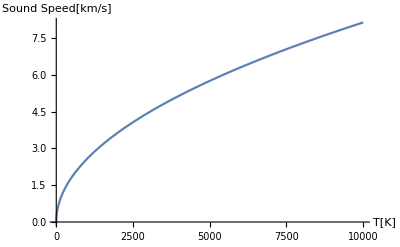

```mathematica
Plot[csT[T], {T,0,10000}, AxesLabel->{"T[K]","Sound Speed[km/s]"}]
```

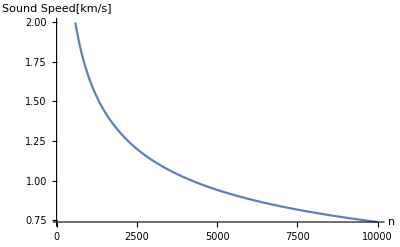

```mathematica
Plot[csn[n], {n,100,10000}, AxesLabel->{"n","Sound Speed[km/s]"}]
```

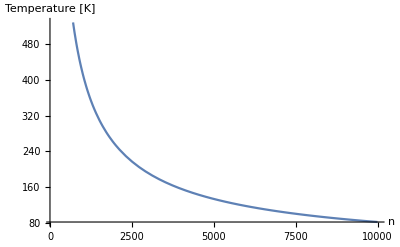

```mathematica
Plot[Tn[n],  {n,100,10000}, AxesLabel->{"n","Temperature [K]"}]
```

## Define Delta T

```mathematica
Deltat[cs_, csin_]:=csin^2/cs^2
```

## Threshold Velocities

```mathematica
MdT[Tout_, Tin_]:=Sqrt[Tin/Tout]*(1-Sqrt[1-(Tout/Tin)])
MrT[Tout_, Tin_]:=Sqrt[Tin/Tout]*(1+Sqrt[1-(Tout/Tin)])
```

```mathematica
Plot[{MdT[T,Tcs[25]], MrT[T, Tcs[25]]}, {T, 1, 10^5}, PlotLabels->{"M_d","M_r"}, AxesLabel->{"T out [K]","Mach"}]
```

-Graphics-

```mathematica
Md[cs_, csin_]:=Sqrt[Deltat[cs, csin]]*(1-Sqrt[1-(1/Deltat[cs, csin])])
Mr[cs_, csin_]:=Sqrt[Deltat[cs, csin]]*(1+Sqrt[1-(1/Deltat[cs, csin])])
```

```mathematica
pl1=Plot[{Md[cs, 25], Mr[cs,25]}, {cs, .1, 30}, PlotLabels->{"M_d","M_r"}, AxesLabel->{"local Sound Speed [km/s]","Mach"}]
```

-Graphics-

```mathematica
pl2=Plot[{Md[c, 10], Mr[c, 10]}, {c, .1, 10}, PlotLabels->{"M_d","M_r"}, AxesLabel->{"local Sound Speed [km/s]","Mach"}]
```

-Graphics-

```mathematica
Show[{pl1, pl2}, PlotLabel->"Mr and Md fos csin = 25 and 10 km/s"]
```

-Graphics-

```mathematica
Plot[{MrT[T],2*Sqrt[ Deltat[csT[T]]]}, {T, 1, 10^5}, PlotLabels->{"M_d","Aprrox"}, AxesLabel->{"T out [K]","Mach"}]
```

-Graphics-

## Delta

```mathematica
Mach[v_, cs_]:=v/cs
Delta[v_, cs_, csin_]:= (1+Mach[v, cs]^2)^2-4*Mach[v, cs]^2*Deltat[cs, csin]
```

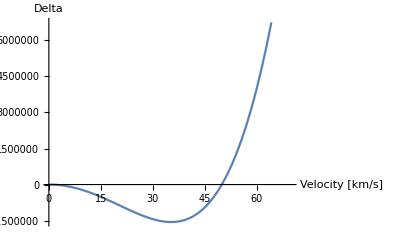

```mathematica
Plot[Delta[v, 1,25], {v,0,70}, AxesLabel->{"Velocity [km/s]","Delta"}]
```

## Delta Rho

```mathematica
vd[cs_, csin_]:=Md[cs, csin]*cs     
vr[cs_, csin_]:=Mr[cs, csin]*cs
```

```mathematica
N[vr[.5,25]]
```

49.995

```mathematica
Deltarhoplus[v_, cs_, csin_]:= (1+Mach[v, cs]^2+Sqrt[Delta[v, cs, csin]])/(2*Deltat[cs, csin])
Deltarhominus[v_, cs_, csin_]:= (1+Mach[v, cs]^2-Sqrt[Delta[v, cs, csin]])/(2*Deltat[cs, csin])
Deltarhozero[v_, cs_, csin_]:= (1+Mach[v, cs]^2)/(2*Deltat[cs, csin])
```

```mathematica
Plot[{Deltarhoplus[v, 1, 10],Deltarhominus[v, 1, 10], Deltarhozero[v, 1, 10]} , {v,0, vd[1,10]},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"}]
```

-Graphics-

```mathematica
Plot[{Deltarhoplus[v, 1, 10],Deltarhominus[v, 1, 10], Deltarhozero[v, 1, 10]} , {v,vr[1,10], 100},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"}]
```

-Graphics-

```mathematica
pl3=Plot[{Deltarhoplus[v, 1, 10],Deltarhominus[v, 1, 10], Deltarhozero[v, 1, 10]} , {v,0, 50},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"}]
```

-Graphics-

```mathematica
pl4=Plot[{Deltarhoplus[v, 1, 12],Deltarhominus[v, 1, 12], Deltarhozero[v, 1, 12]} , {v,0, 50},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"}];
```

```mathematica
Show[{pl3,pl4}, PlotRange->{Automatic,{0,5}}, PlotLabel-> "Delta rho for csin=10 and 12 km/s"]
```

-Graphics-

-Graphics-

```mathematica
Plot[{Deltarhoplus[v, 1,10],Deltarhominus[v, 1, 10], Deltarhozero[v, 1, 10]} , {v,0, 50},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"},  PlotRange->{{0,100},{0,5}}]
```

-Graphics-

```mathematica
Plot[{Deltarhoplus[v, .5, 25],Deltarhominus[v, .5, 25], Deltarhozero[v, .5, 25]} , {v,0, 100},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"},  PlotRange->{{0,100},{0,5}}]
```

-Graphics-

## n inside

```mathematica
ninplus[v_, cs_, n_, csin_]:= Deltarhoplus[v, cs, csin]*n       (*cm^-3*)
ninminus[v_, cs_, n_, csin_]:= Deltarhominus[v, cs, csin]*n
ninzero[v_, cs_, n_, csin_]:= Deltarhozero[v, cs, csin]*n
```

```mathematica
Plot[{ninplus[v, 1, 10^4, 10],ninminus[v, 1, 10^4, 10], ninzero[v, 1, 10^4, 10]}, {v,0,vd[1,10]},  AxesLabel->{"Velocity [km/s]","n in"}, PlotLabels->{"plus ","minus", "zero"}, PlotLabel->"number density in ionized phase"]
```

-Graphics-

```mathematica
Plot[{ninplus[v, 1, 10^4, 10],ninminus[v, 1, 10^4, 10], ninzero[v, 1, 10^4, 10]}, {v,vr[1,10], 100},  AxesLabel->{"Velocity [km/s]","n in"}, PlotLabels->{"plus ","minus", "zero"}, PlotLabel->"number density in ionized phase"]
```

-Graphics-

```mathematica
Plot[{ninplus[v, 1, 10^4, 10],ninminus[v, 1, 10^4, 10], ninzero[v, 1, 10^4, 10]}, {v,0, 50},  AxesLabel->{"Velocity [km/s]","n in"}, PlotLabels->{"plus ","minus", "zero"}, PlotLabel->"number density in ionized phase"]
```

-Graphics-

## v inside (for n out =10^4)

```mathematica
vinplus[v_, cs_, csin_]:= v/Deltarhoplus[v, cs, csin]
vinminus[v_, cs_, csin_]:= v/Deltarhominus[v, cs, csin]
vinzero[v_, cs_, csin_]:= v/Deltarhozero[v, cs, csin]
```

```mathematica
Plot[{vinplus[v, 1, 10],vinminus[v, 1,10], vinzero[v,1,10]}, {v,0,vd[1,10]},  AxesLabel->{"Velocity [km/s]","V in"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
Plot[{vinplus[v, 1,10],vinminus[v, 1, 10], vinzero[v,1, 10]}, {v,0,2},  AxesLabel->{"Velocity [km/s]","V in"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
Plot[{vinplus[v, 1, 10],vinminus[v, 1, 10], vinzero[v,1, 10]}, {v,0, 50},  AxesLabel->{"Velocity [km/s]","V in"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

## Accretion Rate

```mathematica
(*In units of kg/s*)
```

```mathematica
const=G^2* Exp[1.5]*Pi;
```

```mathematica
Mpeakapprox  = const*(7*Msun)^2/(3*25*1000)^3*2*10^4/cm3*muH2
MBondiapprox= const*(7*Msun)^2/(50*1000)^3*10^4/cm3*muH2
Mdotzero[vr[1,25],10^4, 7*Msun, 1,25]
```

2.61646×10^12

4.41528×10^12

Mdotzero[25 (1+(4 √39)/25),10000,1.3919×10^31,1,25]

```mathematica
rhoinplus[v_,  n_,cs_, csin_]:= ninplus[v,cs, n, csin]/cm3*muH2
rhoinminus[v_,  n_,cs_, csin_]:= ninminus[v,cs, n, csin]/cm3*muH2
rhoinzero[v_,  n_,cs_, csin_]:= ninzero[v, cs, n, csin]/cm3*muH2
```

```mathematica
Mdotplus[v_,  n_,M_, cs_:1, csin_:25]  := const* M^2*((  vinplus[v, cs, csin]*km/s)^2+(csin*km/s)^2)^(-3/2)*rhoinplus[v,n,cs,  csin]
Mdotminus[v_,  n_,M_,  cs_:1, csin_:25] := const*M^2*((vinminus[v, cs, csin]*km/s)^2+(csin*km/s)^2)^(-3/2)*rhoinminus[v, n,cs, csin]
Mdotzero[v_,  n_,M_,  cs_:1, csin_:25]  := const*M^2*((   vinzero[v, cs, csin]*km/s)^2+(csin*km/s)^2)^(-3/2)*rhoinzero[v,  n,cs, csin]
```

```mathematica
Plot[{Mdotplus[v,10^4, 7*Msun, 1, 25],Mdotminus[v,10^4, 7*Msun, 1,25], Mdotzero[v,10^4, 7*Msun, 1, 25]},{v,0,vd[1,25]}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
P3=Plot[{Mdotplus[v,10^4, 7*Msun, .5, 10],Mdotminus[v,10^4, 7*Msun, .5, 10], Mdotzero[v,10^4, 7*Msun, .5, 10]},{v,0,.1}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
LogPlot[{Mdotplus[v,10^4, 7*Msun, .5, 10],Mdotminus[v,10^4, 7*Msun, .5, 10], Mdotzero[v,10^4, 7*Msun, .5, 10]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot [kg/s]"}, PlotLabels->{"plus ","minus", "zero"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
LogPlot[{Mdotplus[v, 10^4,7*Msun]/(Msun/year),Mdotminus[v, 10^4, 7*Msun]/(Msun/year), Mdotzero[v, 10^4, 7*Msun]/(Msun/year)},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot [Msun/year]"}, PlotLabels->{"plus ","minus", "zero"}, PlotRange->Automatic, PlotLabel->"Accretion Rate"]
```

-Graphics-

## Impact of n and cs on accretion rate

```mathematica
P1=Plot[{Mdotplus[v,10^4, 7*Msun, .5, 10],Mdotminus[v,10^4, 7*Msun, .5, 10], Mdotzero[v,10^4, 7*Msun, .5, 10]},{v,0,30}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"},  PlotRange->{{0,30},Automatic}]
```

-Graphics-

```mathematica
P2=Plot[{Mdotplus[v,10^4, 7*Msun, 1, 10],Mdotminus[v,10^4, 7*Msun, 1, 10], Mdotzero[v,10^4, 7*Msun, 1, 10]},{v,0,30}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"},  PlotRange->{{0,30},Automatic}]
```

-Graphics-

```mathematica
Show[{P1,P2},  PlotLabel->" cs=.5 vs cs=1 for high velocity "]
```

-Graphics-

```mathematica
P4=Plot[{Mdotplus[v,10^4, 7*Msun, 1, 10],Mdotminus[v,10^4, 7*Msun, 1, 10], Mdotzero[v,10^4, 7*Msun, 1, 10]},{v,0,.1}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
Show[{P3, P4} ,  PlotLabel->"cs=.5 vs cs=1 for low velocity"]
```

-Graphics-

```mathematica
P5=Plot[{Mdotplus[v,10^3, 7*Msun, .5, 10],Mdotminus[v,10^3, 7*Msun, .5, 10], Mdotzero[v,10^3, 7*Msun, .5, 10]},{v,0,30}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"},  PlotRange->{Automatic,Automatic}]
```

-Graphics-

```mathematica
Show[{P1, P5},   PlotLabel->"n=10^4 vs n=10^3 "]
```

-Graphics-

```mathematica
Plot[{Mdotplus[vr[1,25], n, 7*Msun],Mdotminus[vr[1,25], n, 7*Msun], Mdotzero[vr[1, 25],  n,7*Msun]},{n,10^2,10^4}, AxesLabel->{"n","Mdot"}, PlotLabels->{"plus ","minus", "zero"},  PlotRange->{{10,10000},Automatic},   PlotLabel->"Peak accretion vs n for cs=1 km/s"]
```

-Graphics-

```mathematica
Plot[{Mdotplus[50,  n, 7*Msun],Mdotminus[50,  n,7*Msun], Mdotzero[50,  n,7*Msun]},{n,10^2,10^4}, AxesLabel->{"n","Mdot"}, PlotLabels->{"plus ","minus", "zero"},   PlotLabel->"accretion vs rho for v=50 kms, cs=1 km/s"]
```

-Graphics-

```mathematica
(*derivatives*)
D[Mdotzero[10,  n, 7*Msun], n]   
D[Mdotzero[vr[.5,10], n, 7*Msun], n]
D[Mdotminus[50,n, 7*Msun], n]
```

2.21544×10^6

5.82557×10^7

2.32576×10^9

```mathematica
Plot[{ Mdotzero[vr[cs,10], 10^4, 7*Msun,  cs],  Mdotzero[vr[cs,10], 10^3, 7*Msun,  cs]},{cs,.1,10}, AxesLabel->{"n","Mdot"}, PlotLabels->{"10^4", "10^3"},  PlotRange->{Automatic,Automatic},   PlotLabel->"Peak accretion vs cs for n= 10^4, 10^3"]
```

-Graphics-

## Impact of Ionized Sound Speed on Accretion Rate

```mathematica
P6=LogPlot[{Mdotplus[v,10^4, 7*Msun, 1, 10],Mdotminus[v,10^4, 7*Msun, 1, 10], Mdotzero[v,10^4, 7*Msun, 1, 10]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
P7=LogPlot[{Mdotplus[v,10^4, 7*Msun, 1, 25],Mdotminus[v,10^4, 7*Msun, 1, 25], Mdotzero[v,10^4, 7*Msun, 1, 25]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
Show[{P6,P7}, PlotLabel-> "Accretion Rate for csin= 10 and 25 km/s"]
```

-Graphics-

## Comparison with Bondi accretion

```mathematica
MdotBondi[v_,  n_, M_,cs_:1]:= const*M^2*((v*km)^2+(cs*km)^2)^(-3/2)*n/cm3*muH2
```

```mathematica
Plot[{Mdotplus[v, 10^4, 7*Msun],Mdotminus[v, 10^4, 7*Msun], Mdotzero[v,  10^4,7*Msun],  MdotBondi[v, 10^4, 7*Msun]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"Bondi accretion vs Ricotti for n= 10^4"]
```

-Graphics-

```mathematica
LogPlot[{Mdotplus[v, 10^4, 7*Msun],Mdotminus[v, 10^4, 7*Msun], Mdotzero[v,  10^4,7*Msun],  MdotBondi[v, 10^4, 7*Msun]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"Bondi accretion vs Ricotti for n= 10^4"]
```

-Graphics-

```mathematica
LogPlot[{Mdotplus[v, 10^3, 7*Msun],Mdotminus[v, 10^3, 7*Msun], Mdotzero[v,  10^3,7*Msun],  MdotBondi[v, 10^3, 7*Msun]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"Bondi accretion vs Ricotti for n= 10^3"]
```

-Graphics-

## Luminosity

```mathematica
(*Luminosity in J/s*)
```

```mathematica
eta0=0.1;
(*s=-1.6;
R=Integrate[x^s, {x,10,40}]/Integrate[x^s, {x,2,10}]*)
```

```mathematica
LEddFender= 1.26*10^31* 7;
LEdd[M_]:=1.26*10^31* (M/Msun) (*J/s*)

Mdotcrit[M_]:= 0.01*LEdd[M]/(eta0*c^2)

eta[Mdot_, M_]:= eta0*Mdot/Mdotcrit[M]

LogPlot[{eta[Mdotplus[v,10^4, 7*Msun], 7*Msun],eta[Mdotminus[v,10^4, 7*Msun], 7*Msun],eta[Mdotzero[v,10^4, 7*Msun], 7*Msun]}, {v, 0, 100}, AxesLabel->{"Velocity [km/s]","eta"}, PlotLabels->{"plus ","minus", "zero"}, PlotRange->{Automatic, {0.001, .1}}]
```

-Graphics-

```mathematica
LX[Mdot_, M_, k_]:=k*eta[Mdot,M]*Mdot*c^2
```

```mathematica
(* flux in J/s/m^2 *)
```

```mathematica
Fxminus[v_, n_, M_,d_, cs_:1, csin_:25, k_:0.3]:=LX[Mdotminus[v, n, M, cs, csin], M, k]/(4*Pi*d^2)
Fxplus[v_, n_, M_,d_, cs_:1, csin_:25, k_:0.3]:=LX[Mdotplus[v, n, M, cs, csin], M, k]/(4*Pi*d^2)
Fxzero[v_, n_, M_,d_, cs_:1, csin_:25, k_:0.3]:=LX[Mdotzero[v, n, M, cs, csin], M, k]/(4*Pi*d^2)
FxBondi[v_, n_, M_,d_, cs_:1, csin_:25, k_:0.3]:=LX[MdotBondi[v, n, M, cs], M, k]/(4*Pi*d^2)
```

```mathematica
(*debug*)
Mdotcrit[7*Msun]
Mdotzero[50, 10^4, 7*Msun]
eta[Mdotzero[50, 10^4, 7*Msun], 7*Msun]
LX[Mdotzero[50, 10^4, 7*Msun, 1, 25], 7*Msun]
LX[Mdotzero[50, 10^4, 7*Msun], 7*Msun]
LX[Mdotzero[50, 10^4, 7*Msun], 7*Msun]/(4*Pi*(8*kpc)^2)
Fxzero[50, 10^4, 7*Msun, 8*kpc]
Fxzero[50, 10^4, 7*Msun, 8*kpc, 1, 25]
```

```mathematica
LX[Mdotzero[50, 10^4, 7*Msun, 1, 25], 7*Msun]/LEdd[7*Msun]
```

0.000194715

```mathematica
Mdotzero[50,10^4, 7*Msun]/Mdotcrit[7*Msun]
```

0.254764

```mathematica
LogPlot[{Fxplus[v, 10^4,7*Msun, 8*kpc],Fxminus[v, 10^4,7*Msun, 8*kpc], Fxzero[v, 10^4,7*Msun, 8*kpc], FxBondi[v, 10^4,7*Msun, 8*kpc]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Flux[J/s/m^2]"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"Bondi accretion vs Ricotti for n= 10^4"]
```

-Graphics-

```mathematica
(*convert from J/s/m^2 to cgs, ie erg/s/cm^2*)
erg=10^-7;
```

```mathematica
LogPlot[{Fxplus[v, 10^4,7*Msun, 8*kpc]/(erg/cm^2),Fxminus[v, 10^4,7*Msun, 8*kpc]/(erg/cm^2), Fxzero[v, 10^4,7*Msun, 8*kpc]/(erg/cm^2), FxBondi[v, 10^4,7*Msun, 8*kpc]/(erg/cm^2)},{v,10,400}, PlotRange->{Automatic, {10^-20, 10^-8}}, AxesLabel->{"Velocity [km/s]","Flux[erg/s/cm^2]"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"X-ray Flux for n= 10^4"]
```

-Graphics-

## Define the Flux piecewise

```mathematica
Flux[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=Piecewise[{{Fxplus[v, n,M, d, cs, csin, k], v< vd[cs,csin]}, {Fxzero[v, n,M, d, cs, csin, k], vd[cs,csin]<=v<=vr[cs,csin]}, {Fxminus[v, n,M, d, cs, csin, k], v>= vr[cs,csin]}}]
```

3.35292×10^-11

204.019

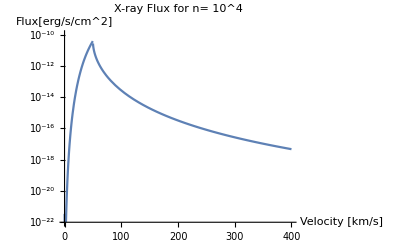

```mathematica
LogPlot[Flux[v, 10^4,8.4*Msun, 8*kpc]/(erg/cm^2), {v,0,400}, AxesLabel->{"Velocity [km/s]","Flux[erg/s/cm^2]"}, PlotLabel->"X-ray Flux for n= 10^4", PlotRange->{Automatic, {10^-22, 10^-10}}]
```

```mathematica
Flux[150, 10^3,7*Msun, 8.3, 1, 25]
```

9.80833×10^18

## Define the Radio Flux using the fundamental plane

```mathematica
Lx[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:= Flux[v, n,M, d, cs, csin, k]*(4*Pi*d^2)
```

Using the fundamental plane values for luminosities in ergs. Must convert to erg and then back to Joules.

```mathematica
a1=1.45;
a2=0.88;
a3=6.07;
```

```mathematica
Lr[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=10^((Log[10, Lx[v, n,M, d, cs, csin, k]/erg]+a2*Log[10, M/Msun]+a3)/a1)*erg;
LrBondi[v_, n_,M_, cs_:1,  k_:0.3]:=10^((Log[10, LX[MdotBondi[v, n, M, cs], M, k]/erg]+a2*Log[10, M/Msun]+a3)/a1)*erg;
```

This is in Joules/s/m^2:

```mathematica
RFlux1[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=Lr[v, n,M, d, cs, csin, k]/(4*Pi*(d)^2);
RFlux1Bondi[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=LrBondi[v, n,M,  cs,  k]/(4*Pi*(d)^2);
```

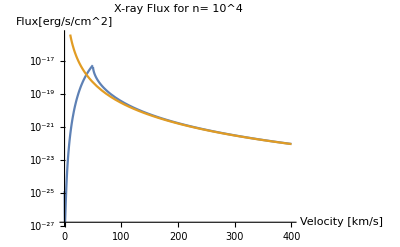

```mathematica
LogPlot[{ RFlux1[v, 10^4,5*Msun, 8*kpc]/(erg/cm^2), RFlux1Bondi[v, 10^4,5*Msun, 8*kpc]/(erg/cm^2)}, {v,0,400}, AxesLabel->{"Velocity [km/s]","Flux[erg/s/cm^2]"}, PlotLabel->"X-ray Flux for n= 10^4"]
```

Convert to mJy (first to erg/cm^2 then to mJy)

```mathematica
obsFrequency=1.4*10^9;
Jyergconversion=10^-23;
```

```mathematica
RFlux[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=RFlux1[v, n,M, d, cs, csin, k]/(erg/cm^2)*1000/obsFrequency/Jyergconversion
RFluxBondi[v_, n_,M_, d_, cs_:1, k_:0.3]:=RFlux1Bondi[v, n,M, d, cs,  k]/(erg/cm^2)*1000/obsFrequency/Jyergconversion
```

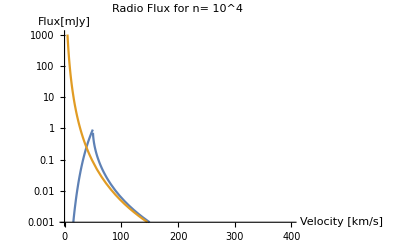

```mathematica
LogPlot[{ RFlux[v, 10^4,7*Msun, 8*kpc], RFluxBondi[v, 10^4,7*Msun, 8*kpc]}, {v,0,400}, AxesLabel->{"Velocity [km/s]","Flux[mJy]"}, PlotLabel->"Radio Flux for n= 10^4", PlotRange->{Automatic, {10^-3, 10^3}}]
```

Compare X and Radio bands

```mathematica
LogPlot[{ RFlux1[v, 10^4,5*Msun, 8*kpc]/(erg/cm^2), Flux[v, 10^4,5*Msun, 8*kpc]/(erg/cm^2)}, {v,0,400}, AxesLabel->{"Velocity [km/s]","Flux[erg/s/cm^2]"}, PlotLabel->"X-ray vs Radio Flux for n= 10^4", PlotLabels->{"Radio", "Xray"}]
```

-Graphics-

## Plot dependence of X-Flux on parameters

```mathematica
labelv=DisplayForm[RowBox[{StyleBox["Velocity",FontSize->30],StyleBox["   [km/s]",FontSize->25]}]];
labelcs=DisplayForm[RowBox[{StyleBox[SubscriptBox["C","s"],FontSize->30],StyleBox[" [km/s]",FontSize->25]}]];
labelcsin=DisplayForm[RowBox[{StyleBox[SuperscriptBox[SubscriptBox["C","s"],"in"],FontSize->30],StyleBox[" [km/s]",FontSize->25]}]];
labelrho=DisplayForm[RowBox[{StyleBox["ρ",FontSize->30],StyleBox[RowBox[{"[", SuperscriptBox["cm", "-3"], "]"}],FontSize->25]}]];
labelXflux=DisplayForm[RowBox[{StyleBox["X-ray flux",FontSize->30],StyleBox["   [erg/cm^2/s]",FontSize->25]}]];

CMZTitle=DisplayForm[StyleBox["ABHs in CMZ Molecular Clouds",FontSize->30]];

fticksL=Table[Which[IntegerQ[Log[10,i]/2],{i,DisplayForm[StyleBox[SuperscriptBox["10",Log[10,i]],FontSize->20]],{.018,0},Black},
IntegerQ[Log[10,i]],{i,,{.018,0},Black},
True,{i,"",{.007,0},Black}],{i,Flatten[Table[10^j*k,{j,-27,-.1},{k,1,9}]]}];

fticksD= Table[If[IntegerQ[i/50],{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,0,400,10}];
ftickscs= Table[{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{i,0,1.5,0.1}];
ftickscsin= Table[If[IntegerQ[i/10],{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,0,50,5}];
fticksrho= Table[If[IntegerQ[Log[10,i]],{i,DisplayForm[StyleBox[SuperscriptBox["10",Log[10,i]],FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,Flatten[Table[10^j*k,{j,1,5},{k,1,9}]]}];
```

```mathematica
ColorData[1,"ColorList"]
```

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.42664098839727194, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24],RGBColor[0.24, 0.47354534880363613, 0.6],RGBColor[0.5163614825959097, 0.24, 0.6],RGBColor[0.6, 0.3062683139954558, 0.24],RGBColor[0.3838248546049982, 0.6, 0.24],RGBColor[0.24, 0.5939180232054561, 0.6],RGBColor[0.39598880819409377, 0.24, 0.6],RGBColor[0.6, 0.24, 0.2941043604063603]}

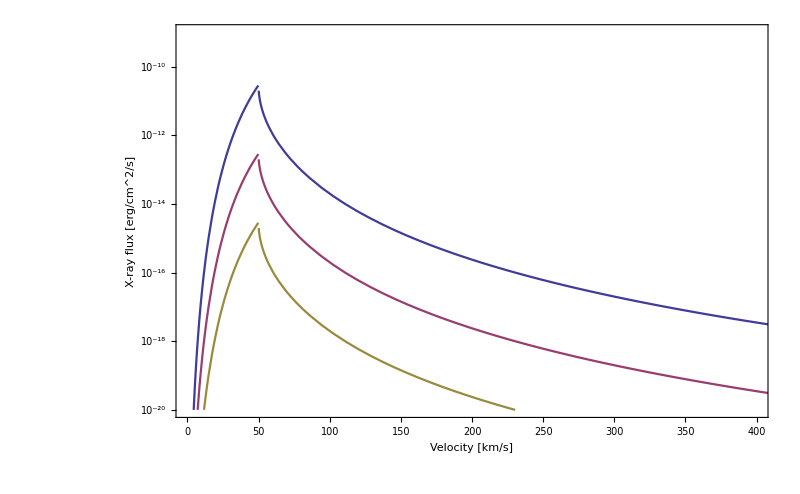

```mathematica
Legended[
LogPlot[
{
Flux[v, 10^4,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),Flux[v, 10^3,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2), Flux[v, 10^2,7.8*Msun,8.3*kpc, 1]/(erg/cm^2)
,NustarBound},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-20, 10^-9}},
FrameLabel->{labelv,labelXflux}, 
ImageSize->800, 
PlotStyle->ColorData[1,"ColorList"],
FrameTicks->{{fticksL, None},{fticksD, None}},
GridLines->{Table[50*i,{i,40}],Automatic}
],

 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"ρ= 10^4 cm^-3" , "ρ= 10^3 cm^-3", "ρ= 10^2 cm^-3"}],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

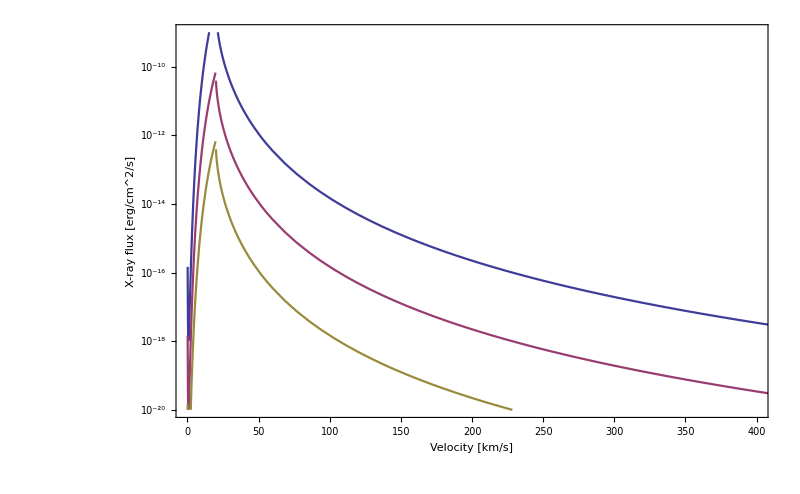

```mathematica
Legended[
LogPlot[
{
Flux[v, 10^4,7.8*Msun, 8.3*kpc, 1, 10]/(erg/cm^2),Flux[v, 10^3,7.8*Msun, 8.3*kpc, 1, 10]/(erg/cm^2), Flux[v, 10^2,7.8*Msun,8.3*kpc, 1, 10]/(erg/cm^2)
,NustarBound},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-20, 10^-9}},
FrameLabel->{labelv,labelXflux}, 
ImageSize->800, 
PlotStyle->ColorData[1,"ColorList"],
FrameTicks->{{fticksL, None},{fticksD, None}},
GridLines->{Table[50*i,{i,40}],Automatic}
],

 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"ρ= 10^4 cm^-3" , "ρ= 10^3 cm^-3", "ρ= 10^2 cm^-3"}],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

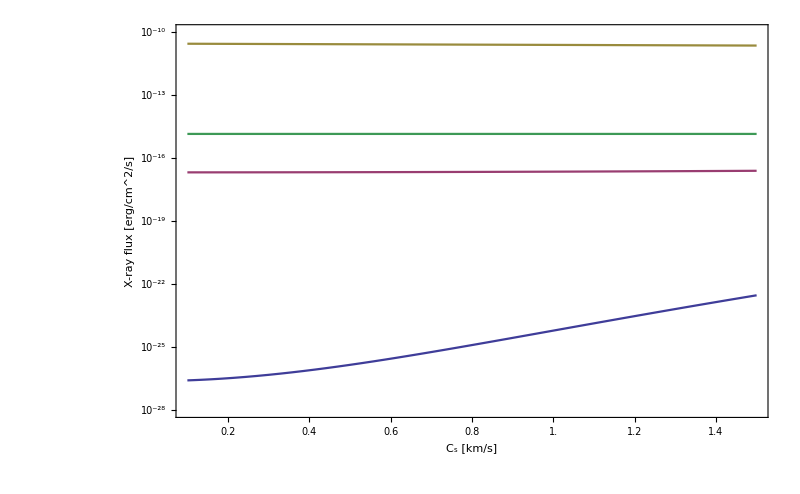

```mathematica
Legended[
LogPlot[
{Flux[1, 10^4,7.8*Msun, 8.3*kpc, cs]/(erg/cm^2),
Flux[10, 10^4,7.8*Msun, 8.3*kpc, cs]/(erg/cm^2),
Flux[50, 10^4,7.8*Msun, 8.3*kpc, cs]/(erg/cm^2),
Flux[150, 10^4,7.8*Msun, 8.3*kpc, cs]/(erg/cm^2)
},
{cs,.1,1.5}, 
Frame->True,
PlotRange->{{0.1,1.5},{10^-28, 10^-10}},
PlotStyle->ColorData[1,"ColorList"],
FrameLabel->{labelcs,labelXflux}, 
ImageSize->800, 
PlotStyle->{{Automatic}, {Dashed}, {Automatic}},
FrameTicks->{{fticksL, None},{ftickscs, None}},
GridLines->{Table[50*i,{i,40}],Automatic}
],

 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"v= 1 km/s" ,"v= 10 km/s", "v= 50 km/s","v= 150 km/s"}],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

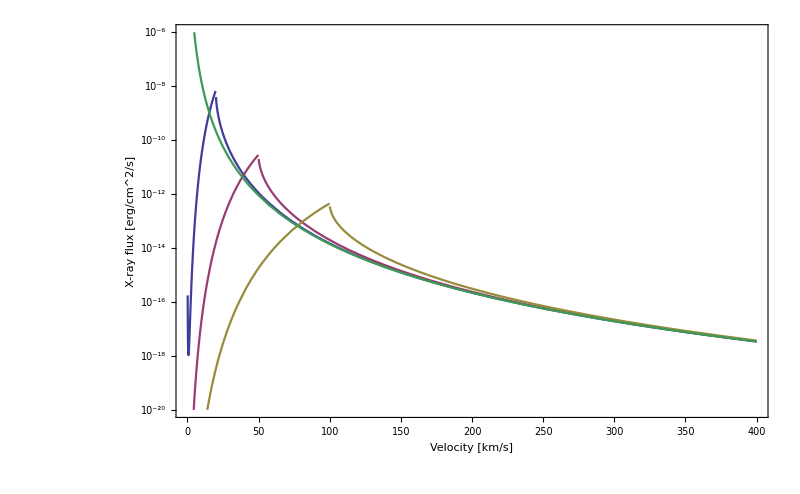

```mathematica
Legended[
LogPlot[
{Flux[v, 10^4,7.8*Msun, 8.3*kpc, 1, 10]/(erg/cm^2),
Flux[v, 10^4,7.8*Msun, 8.3*kpc, 1, 25]/(erg/cm^2),
Flux[v, 10^4,7.8*Msun, 8.3*kpc, 1, 50]/(erg/cm^2),
FxBondi[v, 10^4,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),
NustarBound
},
{v,0,400}, 
Frame->True,
PlotStyle->ColorData[1,"ColorList"],
PlotRange->{{0,400},{10^-20, 10^-6}},
FrameLabel->{labelv,labelXflux}, 
ImageSize->800, 
PlotStyle->{{Automatic}},
FrameTicks->{{fticksL, None},{fticksD, None}},
GridLines->{Table[50*i,{i,40}],Automatic}
],
 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"cs_in= 10 km/s" ,"cs_in= 25 km/s" ,"cs_in= 50 km/s" ,"Bondi"}],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

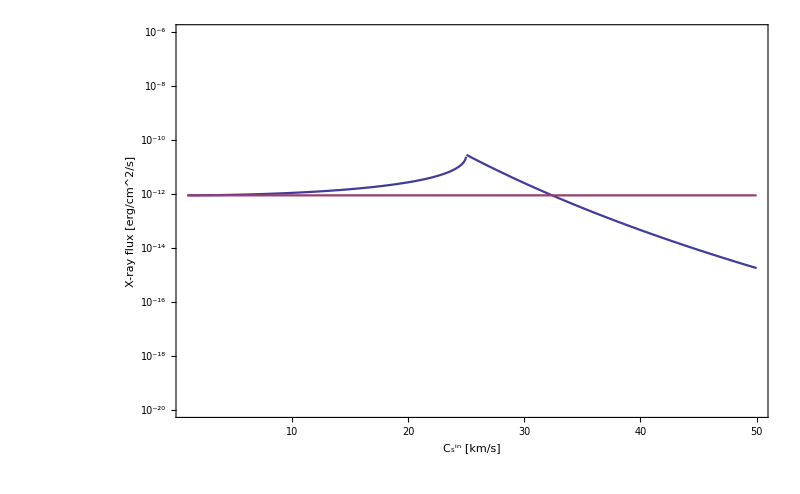

```mathematica
Legended[
LogPlot[
{Flux[50, 10^4,7.8*Msun, 8.3*kpc, 1, csin]/(erg/cm^2),
FxBondi[50, 10^4,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2)
},
{csin,1,50}, 
Frame->True,
PlotRange->{{1,50},{10^-20, 10^-6}},
FrameLabel->{labelcsin,labelXflux}, 
ImageSize->800, 
PlotStyle->ColorData[1,"ColorList"],
FrameTicks->{{fticksL, None},{ftickscsin, None}},
GridLines->{Automatic,Automatic}
],
 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"Ricotti" ,"Bondi"}],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

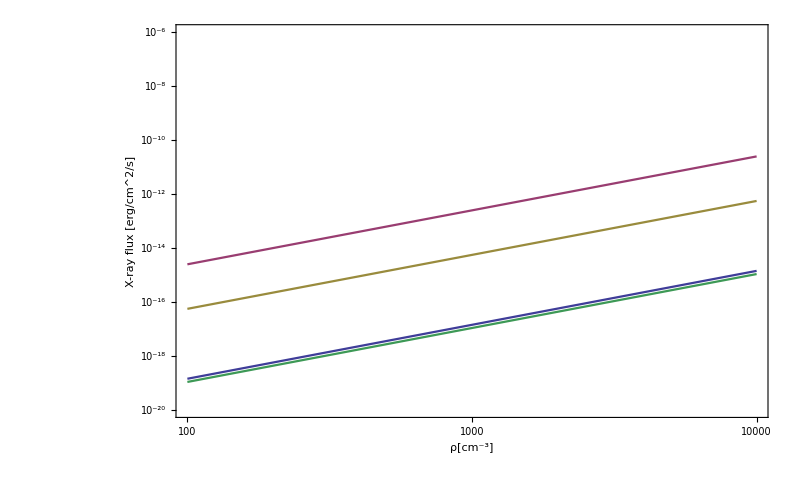

```mathematica
Legended[
LogLogPlot[

{Flux[150,rho ,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),
Flux[50,rho ,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),
Flux[30,rho ,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),
Flux[15,rho ,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),

NustarBound
},
{rho,10^2,10^4}, 
Frame->True,
PlotRange->{{10^2,10^4},{10^-20, 10^-6}},
PlotStyle->ColorData[1,"ColorList"],
FrameLabel->{labelrho,labelXflux}, 
ImageSize->800, 
PlotStyle->{{Automatic}},
FrameTicks->{{fticksL, None},{fticksrho, None}},
GridLines->{Automatic,Automatic}
],
 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"v= 150 km/s","v= 50 km/s" ,"v= 30 km/s" ,"v= 15 km/s" }],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

## Apply the model to ABHs

## Plot accretion rate vs velocity

Find the 1st and 99th percentile of the mass distribution :

```mathematica
mumass=7.8;
sigmamass=1.2;
(mumass-3*sigmamass)
(mumass+3*sigmamass)
(mumass-5*sigmamass)
(mumass+5*sigmamass)
Mmin=(mumass-3*sigmamass)*Msun;
Mmax=(mumass+3*sigmamass)*Msun;

Mmin2=(mumass-3*sigmamass)*Msun;
Mmax2=(mumass+3*sigmamass)*Msun;
```

4.2

11.4

1.8

13.8

```mathematica
mumass-2.32635*sigmamass
```

5.00838

### X-ray flux from CMZ clouds

```mathematica
Dmin=8*kpc
Dmax=8.6*kpc


NustarBound=10^-13;
NustarText=DisplayForm[StyleBox["Nustar" ,FontSize->20,Darker[Red], Opacity[.8],FontFamily->"Times"]];
VLAText=DisplayForm[StyleBox["VLA" ,FontSize->20,Darker[Red], Opacity[.8],FontFamily->"Times"]];
SKAText=DisplayForm[StyleBox["SKA" ,FontSize->20,Darker[Red], Opacity[.8],FontFamily->"Times"]];

RhoText1=DisplayForm[RowBox[{StyleBox[SubscriptBox["n", "∞"],FontSize->20,FontFamily->"Times", Opacity[.8]],StyleBox[" = ",FontSize->20,FontFamily->"Times",  Opacity[.8]], StyleBox[SuperscriptBox["10", "3.5"],FontSize->20,FontFamily->"Times",  Opacity[.8]],
StyleBox[SuperscriptBox["cm", "-3"],FontSize->20,FontFamily->"Times",   Opacity[.8]]
}]];

RhoText2=DisplayForm[RowBox[{StyleBox[SubscriptBox["n", "∞"],FontSize->20,FontFamily->"Times",  Opacity[.8]],StyleBox[" = ",FontSize->20,FontFamily->"Times",  Opacity[.8]], StyleBox[SuperscriptBox["10", "2.5"],FontSize->20,FontFamily->"Times", Opacity[.8]],
StyleBox[SuperscriptBox["cm", "-3"],FontSize->20,FontFamily->"Times",  Opacity[.8]]
}]];




LabelBondi = DisplayForm[StyleBox["Bondi, λ = 1",FontSize->20,FontFamily->"Times",Blue, Opacity[.7]]]
LabelRicotti = DisplayForm[StyleBox["Ricotti",FontSize->20,FontFamily->"Times",Red, Opacity[.7]]]
labelf=Column[{LabelBondi, LabelRicotti},Center]



labelv=DisplayForm[RowBox[{StyleBox["BH speed",FontSize->30],StyleBox["   [km/s]",FontSize->25]}]];
labelavv=DisplayForm[RowBox[{StyleBox["Average Speed",FontSize->30],StyleBox["   [km/s]",FontSize->25]}]];
labelXflux=DisplayForm[RowBox[{StyleBox["X-ray flux",FontSize->30],StyleBox["   [erg/cm^2/s]",FontSize->25]}]];
labelRadioflux=DisplayForm[RowBox[{StyleBox["Radio flux",FontSize->30],StyleBox["   [mJy]",FontSize->25]}]];

CMZTitle=DisplayForm[StyleBox["ABHs in CMZ Molecular Clouds",FontSize->30]];

fticksL=Table[Which[IntegerQ[Log[10,i]/2],{i,DisplayForm[StyleBox[SuperscriptBox["10",Log[10,i]],FontSize->20]],{.018,0},Black},
IntegerQ[Log[10,i]],{i,,{.018,0},Black},
True,{i,"",{.007,0},Black}],{i,Flatten[Table[10^j*k,{j,-27,3},{k,1,9}]]}];

fticksD= Table[If[IntegerQ[i/50],{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,0,400,10}];
```

2.4688×10^20

2.65396×10^20

Bondi, λ = 1

Ricotti

Bondi, λ = 1
Ricotti

```mathematica
Framed[labelf,Background->White,RoundingRadius->5]
```

Bondi, λ = 1
Ricotti

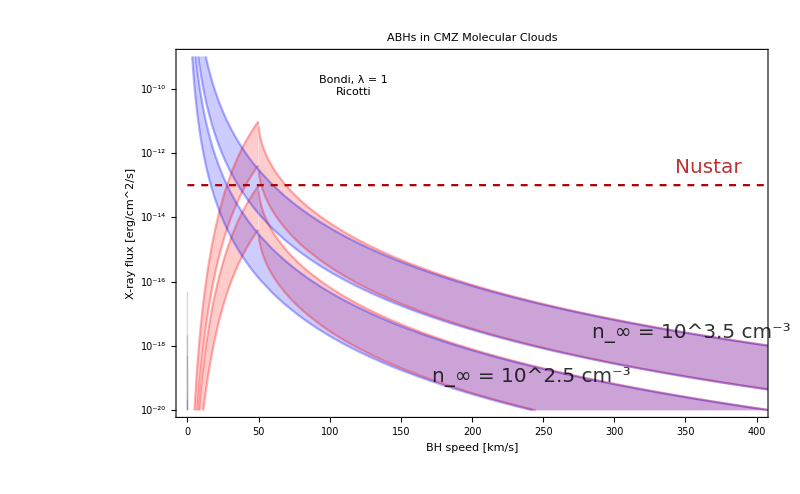

```mathematica
Legended[
LogPlot[
{
Flux[v, 10^3.5,Mmin, Dmax]/(erg/cm^2), Flux[v, 10^3.5,Mmax, Dmin]/(erg/cm^2), 
Flux[v, 10^2.5,Mmin, Dmax]/(erg/cm^2), Flux[v, 10^2.5,Mmax, Dmin]/(erg/cm^2),
FxBondi[v, 10^3.5,Mmin, Dmax]/(erg/cm^2), FxBondi[v, 10^3.5,Mmax, Dmin]/(erg/cm^2), 
FxBondi[v, 10^2.5,Mmin, Dmax]/(erg/cm^2), FxBondi[v, 10^2.5,Mmax, Dmin]/(erg/cm^2),
NustarBound },
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-20, 10^-9}},
FrameLabel->{labelv,labelXflux}, 
PlotLabel->CMZTitle,
ImageSize->800, 
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,4}],Table[{Blue, Opacity[.3]}, {i,4}], {Directive [Darker[Red], Dashed]}], 
Filling->Table[2*i-1->{2*i}, {i,4}],
FrameTicks->{{fticksL, None},{fticksD, None}},
GridLines->{Table[50*i,{i,40}],Automatic}
],
{Placed[NustarText,{.9,.68}],
Placed[RhoText1,{.87,.23}],
Placed[RhoText2,{.6,.11}],
 Placed[Framed[labelf,Background->White,RoundingRadius->5], {.30,.9}]}
]
```

#### Rough estimate of sources above threshold. Assuming around 3000 BH in the most dense CMZ clouds. Including velocities between 35 and 60 km/s.

```mathematica
N[130/Sqrt[8/Pi]]
N[75/Sqrt[8/Pi]]
```

81.4654

46.9993

```mathematica
sigmav=Sqrt[80^2+50^2]
pofv[x_]:=PDF[MaxwellDistribution[sigmav], x];
```

10 √89

```mathematica
N[sigmav]
```

94.3398

```mathematica
vminCMZ=35;
vmaxCMZ=60;
```

```mathematica
N[Integrate[Pofv[x], {x,vminCMZ,vmaxCMZ}]]
```

NIntegrate::inumr: The integrand Pofv[x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{35,60}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[Pofv[x],{x,35,60}]

### X-ray flux from the nearest black holes, following Fender & Maccarone

```mathematica
DFmin=0.07*kpc
DFmax=0.25*kpc

FenderBound=10^-11;
FenderText=DisplayForm[StyleBox["Fender's bound" ,FontSize->20,Darker[Red], Opacity[.8],FontFamily->"Times"]];

RhoText3=DisplayForm[RowBox[{StyleBox[" n = ",FontSize->20,FontFamily->"Times", Opacity[.8]], StyleBox[SuperscriptBox["10", "3"],FontSize->20,FontFamily->"Times", Opacity[.8]],
StyleBox[SuperscriptBox["cm", "-3"],FontSize->20,FontFamily->"Times", Opacity[.8]]
}]];

RhoText4=DisplayForm[RowBox[{StyleBox[" n = ",FontSize->20,FontFamily->"Times", Opacity[.8]], StyleBox[SuperscriptBox["10", "2"],FontSize->20,FontFamily->"Times",  Opacity[.8]],
StyleBox[SuperscriptBox["cm", "-3"],FontSize->20,FontFamily->"Times", Opacity[.8]]
}]];


FenderTitle=DisplayForm[StyleBox["Nearest 250 pc (Fender)",FontSize->30]];
```

2.1602×10^18

7.715×10^18

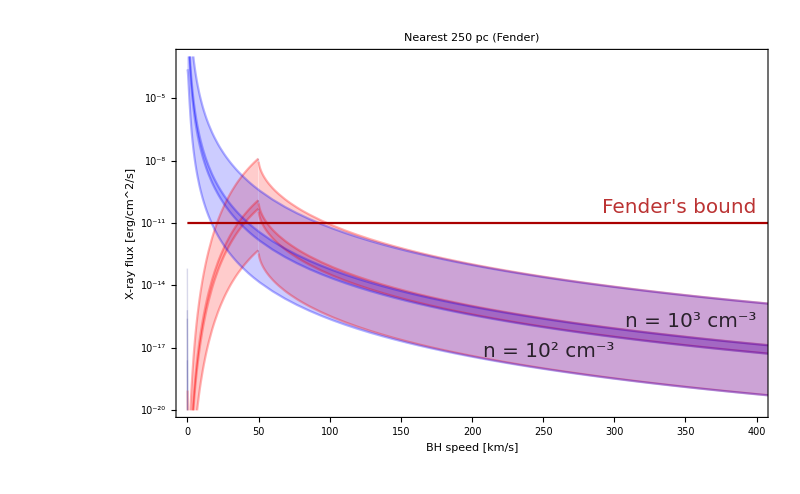

```mathematica
Legended[
LogPlot[{
Flux[v, 10^3,Mmin, DFmax]/(erg/cm^2), Flux[v, 10^3,Mmax, DFmin]/(erg/cm^2), 
Flux[v, 10^2,Mmin, DFmax]/(erg/cm^2), Flux[v, 10^2,Mmax, DFmin]/(erg/cm^2),
FxBondi[v, 10^3,Mmin, DFmax]/(erg/cm^2),FxBondi[v, 10^3,Mmax, DFmin]/(erg/cm^2),
FxBondi[v, 10^2,Mmin, DFmax]/(erg/cm^2), FxBondi[v, 10^2,Mmax, DFmin]/(erg/cm^2),
FenderBound },
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-20, 10^-3}},
FrameLabel->{labelv,labelXflux}, 
PlotLabel->FenderTitle,
ImageSize->800, 
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,4}],Table[{Blue, Opacity[.3]}, {i,4}], {Darker[Red], Opacity[.6]}], 
Filling->Table[2*i-1->{2*i}, {i,4}],
FrameTicks->{{fticksL, None},{fticksD, None}},
GridLines->{Table[50*i,{i,40}],Automatic}
],
{Placed[FenderText,{.85,.57}],
Placed[RhoText3,{.87,.26}],
Placed[RhoText4,{.63,.18}]}
]
```

#### Very rough estimate of sources above threshold. Assuming around 35000 BH in the region. 0.5% in the dense clouds, 5% in the less dense ones.

```mathematica
sigmavF=50; (*neglect dispersion, high kick scenario*)
PofvF[x_]:=PDF[MaxwellDistribution[sigmavF], x];
```

```mathematica
35000*0.005
```

175.

Ricotti case.
1. Dense component.

```mathematica
vminF=30;
vmaxF=70;
```

```mathematica
175*N[Integrate[PofvF[x], {x,vminF,vmaxF}]]
```

64.3345

2. Other component

```mathematica
1/3*1750*N[Integrate[PofvF[x], {x,40,55}]]
```

79.6894

Bondi case

```mathematica
vmaxFB1=65;
vmaxFB2=30;
```

```mathematica
175*N[Integrate[PofvF[x], {x,0,vmaxFB1}]]
1750*N[Integrate[PofvF[x], {x,0,vmaxFB2}]]
```

63.1471

90.3424

Bondi case no kick, lambda=10^-2

```mathematica
vmaxnokick1= 20;
vmaxnokick2= 10;
PofvFnokick[x_]:=PDF[MaxwellDistribution[15], x];

175*N[Integrate[PofvFnokick[x], {x,0,vmaxnokick1}]]
1750*N[Integrate[PofvFnokick[x], {x,0,vmaxnokick2}]]
```

66.538

120.897

### Radio flux vs velocity in the CMZ

```mathematica
VLAbound=1;
SKAsensitivity=10^-6*85
```

17/200000

```mathematica
N[SKAsensitivity]
```

0.000085

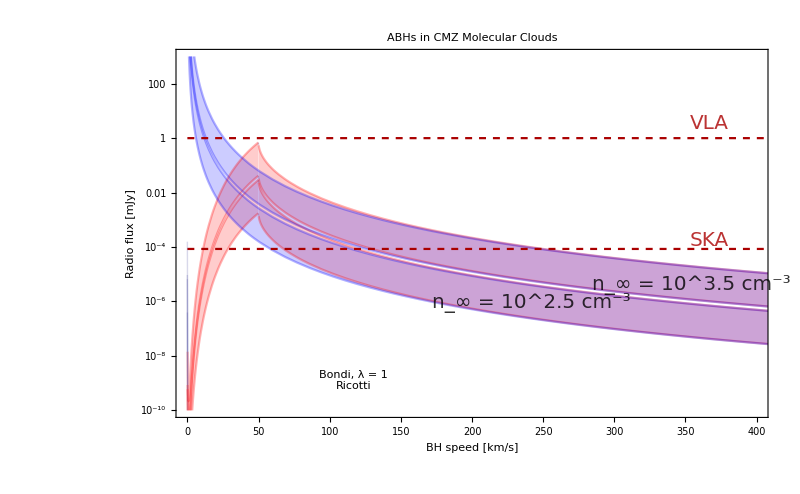

```mathematica
Legended[
LogPlot[
{
RFlux[v, 10^3.5,Mmin, Dmax], RFlux[v, 10^3.5,Mmax, Dmin], 
RFlux[v, 10^2.5,Mmin, Dmax], RFlux[v, 10^2.5,Mmax, Dmin],
RFluxBondi[v, 10^3.5,Mmin, Dmax], RFluxBondi[v, 10^3.5,Mmax, Dmin], 
RFluxBondi[v, 10^2.5,Mmin, Dmax], RFluxBondi[v, 10^2.5,Mmax, Dmin],
VLAbound, SKAsensitivity},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-10, 10^3}},
FrameLabel->{labelv,labelRadioflux}, 
PlotLabel->CMZTitle,
ImageSize->800, 
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,4}],Table[{Blue, Opacity[.3]}, {i,4}], Table[{Directive [Darker[Red], Dashed]}, {i,2}]], 
Filling->Table[2*i-1->{2*i}, {i,4}],
FrameTicks->{{fticksL, None},{fticksD, None}},
GridLines->{Table[50*i,{i,40}],Automatic}
],
{Placed[VLAText,{.9,.80}],
Placed[SKAText,{.9,.48}],
Placed[RhoText1,{.87,.36}],
Placed[RhoText2,{.6,.31}],
 Placed[Framed[labelf,Background->White,RoundingRadius->5], {.30,.1}]}
]
```

## Plot accretion rate vs distance

```mathematica
labeld=DisplayForm[RowBox[{StyleBox["Distance",FontSize->30],StyleBox["   [kpc]",FontSize->25]}]];
```

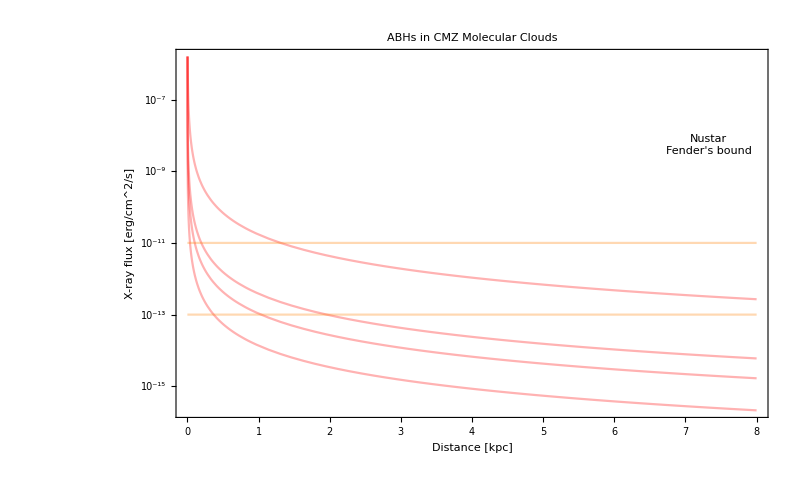

```mathematica
Legended[
LogPlot[
{(*Flux[v, 10^4,Mmin, 8*kpc]/(erg/cm^2), Flux[v, 10^4,Mmax, 8*kpc]/(erg/cm^2),*)
Flux[30, 10^3,mumass*Msun, d*kpc]/(erg/cm^2), Flux[50, 10^3,mumass*Msun, d*kpc]/(erg/cm^2), 
Flux[75, 10^3,mumass*Msun, d*kpc]/(erg/cm^2), Flux[100, 10^3,mumass*Msun, d*kpc]/(erg/cm^2),
(*Flux[10, 10^2,mumass*Msun, d*kpc]/(erg/cm^2), Flux[50, 10^2,mumass*Msun, d*kpc]/(erg/cm^2), 
Flux[75, 10^2,mumass*Msun, d*kpc]/(erg/cm^2), Flux[100, 10^2,mumass*Msun, d*kpc]/(erg/cm^2),*)
NustarBound , FenderBound},
{d,0,8}, 
Frame->True,
PlotRange->{{0,8},Automatic},
FrameLabel->{labeld,labelXflux}, 
PlotLabel->CMZTitle,
ImageSize->800, 
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,4}], Table[{Orange, Opacity[.3]}, {i,4}],{Darker[Red], Opacity[.6]}, {Darker[Red], Opacity[.6]}], 
FrameTicks->{{fticksL, None},{Automatic, None}}
],
{Placed[NustarText,{.9,.74}],
Placed[FenderText,{.9,.74}]
}
]
```

## Bla Bla Contour Plot

```mathematica
InverseFunction[(a #+b)/(c #+d)&]
```

(-b+d #1)/(a-299792000 #1)&

```mathematica
function1[x_]:=(a x+b)/(c x+d)
```

```mathematica
InverseFunction[function1]
```

(-b+d #1)/(a-299792000 #1)&

```mathematica
InverseFunction[function1][3]
```

(-b+3 d)/(-899376000+a)

```mathematica
Integrate[InverseFunction[function1][x], {x,0,100}]
```

ConditionalExpression[-d/2997920+((299792000 b-a d) (Log[29979200000-a]-Log[-a]))/89875243264000000,Re[a]>29979200000||Re[a]<0||a∉Reals]

```mathematica
g=InverseFunction[Function[{x,y},Beta[x,y]-x+y],1,2]
```

InverseFunction[Function[{x,y},Beta[x,y]-x+y],1,2]

```mathematica
g[3,4]
```

Root[{1+Beta[#1,4]-#1&,1.1765901078827981711353549759}]

```mathematica
InverseFunction[#1^2+Log[#2]-1&,2,2]
```

ConditionalExpression[ⅇ^(1-#1^2+#2),-π<Im[-#1^2+#2]≤π]&

```mathematica
InverseFunction[#1^2+Log[#2]-1&,2,1]
```

InverseFunction[#1^2+Log[#2]-1&,2,1]

```mathematica
InverseFunction[#1^2+Log[#2]-1&,1,2]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-√(1-Log[#2]+#1)&

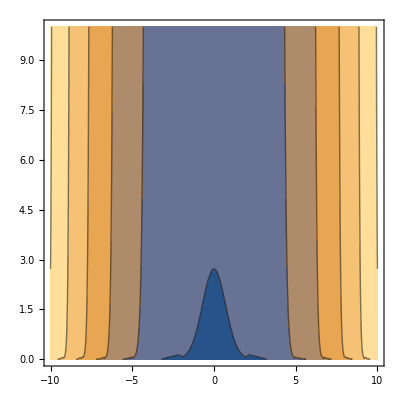

```mathematica
ContourPlot[x^2+Log[y]-1,{x,-10,10},{y,0,10}]
```

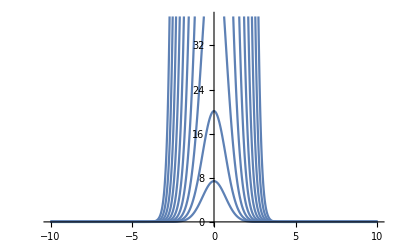

```mathematica
Plot[Table[Exp[-x^2+1+i], {i,10}], {x,-10,10}]
```

```mathematica
Plot[Table[InverseFunction[#1^2+Log[#2]-1&,2,2][x,i], {i,10}], {x,-10,10}]
```

-Graphics-

```mathematica
function3[x_,y_]:=x^2+Log[y]-1
InverseFunction[function3,2,2]
```

ConditionalExpression[ⅇ^(1-#1^2+#2),-π<Im[-#1^2+#2]≤π]&

```mathematica
function4[x_]=InverseFunction[function3,2,2][x, 1]
```

ConditionalExpression[ⅇ^(2-x^2),-π≤Im[x^2]<π]

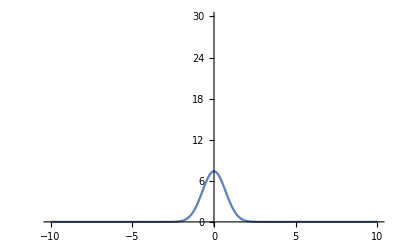

```mathematica
Plot[function4[x],{x,-10,10}, PlotRange->{Automatic,{0,30}}]
```

## Invert Flux expression for M, v

Using inverse function: too slow

```mathematica
(*MassMin[t_, v_, n_, d_, cs_:1, csin_:25]:=InverseFunction[Flux,3, 6][ v, n, d, cs, csin, t]*)
```

```mathematica
(*MassMin[NustarBound, 50, 10^3, .1*kpc]*)
```

```mathematica
(*InverseFunction[Flux,3, 6][ 50, 10^3, .1*kpc, NustarBound]*)
```

Still too slow:

```mathematica
Fluxofvm[v_,m_]:= FxBondi[v, 10^3, m*Msun, .1*kpc]
InverseFunction[Fluxofvm,2, 2]
InverseFunction[Fluxofvm,2, 2][ 50, NustarBound]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

(-39.4317+68.2977 ⅈ) (1.+#1^2) #2^(1/3)&

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-4.57747+7.92842 ⅈ

```mathematica
?? FxBondi
```

Global`FxBondi

FxBondi[v_,n_,M_,d_,cs_:1,csin_:25]:=LX[MdotBondi[v,n,M,cs],M]/(4 π d^2)

```mathematica
FxBondi[x1,x2,x3,x4]
```

(2.46963×10^-48 x2^2 x3^3)/((1000000+1000000 x1^2)^3 x4^2)

```mathematica
Flux[x1,x2,x3,x4, x5, x6]
```

Piecewise[{{(6.17406×10^-49 x2^2 x3^3 x5^4 (1+x1^2/x5^2+√((1+x1^2/x5^2)^2-(4 x1^2 x6^2)/x5^4))^2)/(x4^2 x6^4 (1000000 x6^2+(4000000 x1^2 x6^4)/(x5^4 (1+x1^2/x5^2+√((1+x1^2/x5^2)^2-(4 x1^2 x6^2)/x5^4))^2))^3), x1<x5 (1-√(1-x5^2/x6^2)) √(x6^2/x5^2)}, {(6.17406×10^-49 x2^2 x3^3 (1+x1^2/x5^2)^2 x5^4)/(x4^2 x6^4 (1000000 x6^2+(4000000 x1^2 x6^4)/((1+x1^2/x5^2)^2 x5^4))^3), x5 (1-√(1-x5^2/x6^2)) √(x6^2/x5^2)≤x1≤x5 (1+√(1-x5^2/x6^2)) √(x6^2/x5^2)}, {(6.17406×10^-49 x2^2 x3^3 x5^4 (1+x1^2/x5^2-√((1+x1^2/x5^2)^2-(4 x1^2 x6^2)/x5^4))^2)/(x4^2 x6^4 (1000000 x6^2+(4000000 x1^2 x6^4)/(x5^4 (1+x1^2/x5^2-√((1+x1^2/x5^2)^2-(4 x1^2 x6^2)/x5^4))^2))^3), x1≥x5 (1+√(1-x5^2/x6^2)) √(x6^2/x5^2)}, {0, True}}]

```mathematica
InverseFunction[FxBondi, 3,6]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-((3.69907×10^21+6.40698×10^21 ⅈ) #3^(1/3) #4^(2/3) (#1^2+#5^2))/#2^(2/3)&

```mathematica
-9.102008978137412*^30-1.5765142001082076*^31 ⅈ
FxBondi[##]&
```

-9.10201×10^30-1.57651×10^31 ⅈ

FxBondi[##1]&

```mathematica
Plot[Fluxofvm[v, 10*Msun]/(erg/cm^2), {v, 3,400}]
```

-Graphics-

Try using Nsolve: works!

```mathematica
Fluxofvm[x1,x2]
```

(2.03879×10^12 x2^3)/((1000000+1000000 x1^2)^3)

```mathematica
Solution=NSolve[Fluxofvm[30,x2]== NustarBound && x2>0 , x2, Reals]
```

{{x2→3.29812}}

```mathematica
Mmin=x2/. Solution[[1]]
```

3.29812

```mathematica
MySolution=Function[v,NSolve[Fluxofvm[v,x2]==NustarBound&&x2>0&&v>0,x2,Reals]]
```

Function[v,NSolve[Fluxofvm[v,x2]==NustarBound&&x2>0&&v>0,x2,Reals]]

```mathematica
MySolution[30]
```

{{x2→3.29812}}

```mathematica
Mmin= Function[v,x2/.MySolution[v]]
```

Function[v,x2/.MySolution[v]]

```mathematica
Mmin[30]
```

{3.29812}

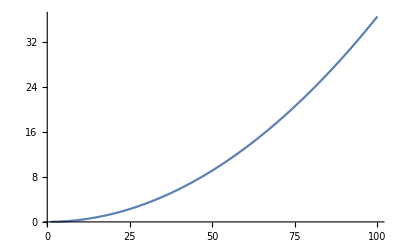

```mathematica
Plot[Mmin[v], {v, 1, 100}]
```

Now try the same with full function:

```mathematica
NewSolution=Function[v,NSolve[FxBondi[v,10^3,x2* Msun, .1 kpc]== NustarBound && x2>0 , x2, Reals]];
NewMmin= Function[v,x2/.NewSolution[v]];
NewMmin[30]
Plot[NewMmin[v], {v, 1, 100}]
```

{3.29812}

-Graphics-

Great! Now try do the same with Ricotti Flux

{1.07335}

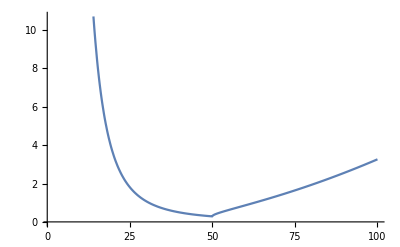

```mathematica
NewSolution2=Function[v,NSolve[Flux[v,10^3,x2* Msun, .1 kpc]/(erg/cm^2)== NustarBound && x2>0 , x2, Reals]];
NewMmin2= Function[v,x2/.NewSolution2[v]];
NewMmin2[30]
Plot[NewMmin2[v], {v, 1, 100}]
```

```mathematica
You can celebrate now !
```

can celebrate You now!

```mathematica
Let' s generalize the definition:
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
MSolution=Function[{v, n, d,cs, csin, t},NSolve[Flux[v,n,x2* Msun, d, cs, csin]/(erg/cm^2)== t && x2>0 , x2, Reals]]
MinMass= Function[{v, n, d, cs, csin, t},x2/.MSolution[v, n, d, cs, csin,t]]
MinMass[30, 10^3, .1 kpc, 1, 25, NustarBound]
Plot[MinMass[v, 10^3, .1*kpc,1, 25, NustarBound], {v, 1, 100}]
```

Function[{v,n,d,cs,csin,t},NSolve[Flux[v,n,x2 Msun,d,cs,csin]/(erg/cm^2)==t&&x2>0,x2,Reals]]

Function[{v,n,d,cs,csin,t},x2/.MSolution[v,n,d,cs,csin,t]]

{1.07335}

-Graphics-

```mathematica
Do the same for the velocity:
```

Syntax::sntxi: Incomplete expression; more input is needed .

Function[{n,m,d,cs,csin,t},NSolve[Flux[x3,n,m,d,cs,csin]/(erg/cm^2)==t&&x3>0,x3,Reals]]

Function[{n,m,d,cs,csin,t},x3/.VSolution[n,m,d,cs,csin,t]⟦1⟧]

Function[{n,m,d,cs,csin,t},x3/.VSolution[n,m,d,cs,csin,t]⟦2⟧]

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

14.2965

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

168.445

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

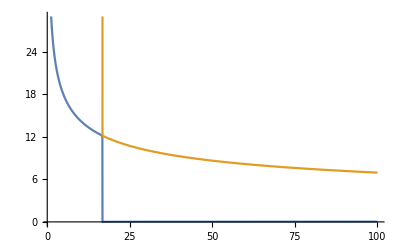

```mathematica
VSolution=Function[{ n, m, d,cs, csin, t},NSolve[Flux[x3, n,m, d, cs, csin]/(erg/cm^2)== t && x3>0 , x3, Reals]]
MinVel= Function[{ n, m,  d, cs, csin, t},x3/.VSolution[ n,m, d, cs, csin,t][[1]]]
MaxVel= Function[{ n, m,  d, cs, csin, t},x3/.VSolution[ n,m, d, cs, csin,t][[2]]]
MinVel[ 10^3, 10*Msun,.1 kpc, 1, 25, NustarBound]
MaxVel[ 10^3, 10*Msun,.1 kpc, 1, 25, NustarBound]
Plot[{MinVel[10^3, m*Msun, .1*kpc,1, 25, NustarBound],MaxVel[10^3, m*Msun, .1*kpc,1, 25, NustarBound]}, {m, 1, 100}]
```

```mathematica
VSolution[ 10^3, 10*Msun,.1 kpc, 1, 25, NustarBound][[2]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{x3→168.445}

```mathematica
Now make some nice plots! And we're done!
```

And make nice re some Mon 15 Jun 2020 16:02:54GMT+2. done! plots! we'

### Plots!

```mathematica
labelm=DisplayForm[RowBox[{StyleBox["Mass",FontSize->30],StyleBox["   [M sun]",FontSize->25]}]];

MinMassCMZTitle=DisplayForm[StyleBox["Minimum mass in CMZ Molecular Clouds (Nustar)",FontSize->30]];

DText=DisplayForm[StyleBox[" d = 8 kpc",FontSize->20,FontFamily->"Times", Bold, Darker[Red], Opacity[.8]]];


fticksL2=Table[If[IntegerQ[i/20],{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,0,100,5}];
fticksD2= Table[If[IntegerQ[i/20],{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,0,300,10}];
```

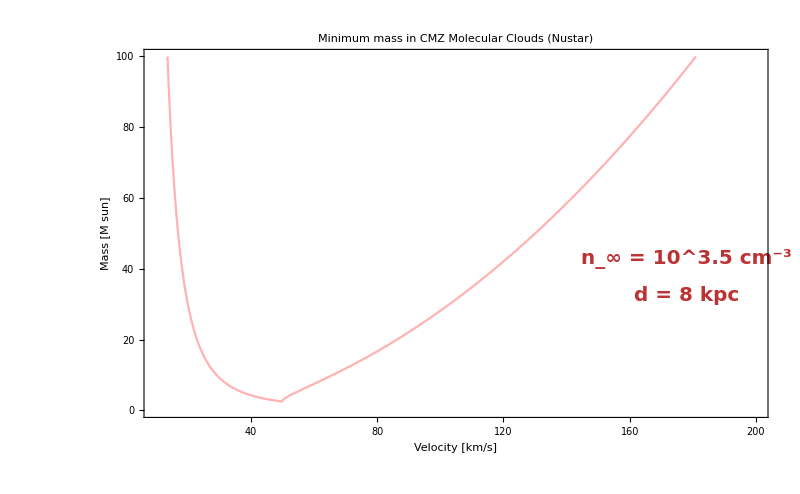

```mathematica
Legended[
Plot[
MinMass[v, 10^3.5, 8*kpc,1, 25, NustarBound], 
{v,10,200}, 
Frame->True,
PlotRange->{{10,200},{0,100}},
FrameLabel->{labelv,labelm}, 
PlotLabel->MinMassCMZTitle,
ImageSize->800, 
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,4}], {Darker[Red], Opacity[.6]}], 
FrameTicks->{{fticksL2, None},{fticksD2, None}}
],

{Placed[RhoText1,{.87,.43}], Placed[DText,{.87,.33}]}

]
```

## Define the PDFs

### Mass

```mathematica
mumass=7.8;
sigmamass=1.2;
```

```mathematica
PofM[x_, mu_:mumass, sigma_:sigmamass]:=PDF[NormalDistribution[mu,sigma],x]
```

### Velocity

```mathematica
muvel= Sqrt[130^2+75^2]
```

5 √901

```mathematica
N[150/Sqrt[8/Pi]]
```

93.9986

```mathematica
Pofv[x_, muv_:muvel]:=PDF[MaxwellDistribution[muv/Sqrt[8/Pi]],x]
```

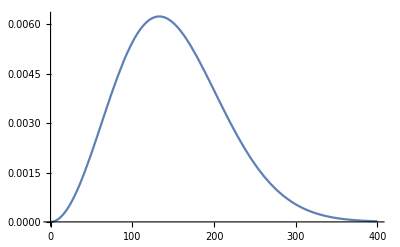

```mathematica
Plot[Pofv[v], {v,0,400}]
```

```mathematica
NIntegrate[Pofv[x, 130], {x, 35,60}]
```

0.0705669

```mathematica
Pofr[r_, rmin_:0.07, rmax_:0.25]:= 3/(rmax^3-rmin^3)*r^2
```

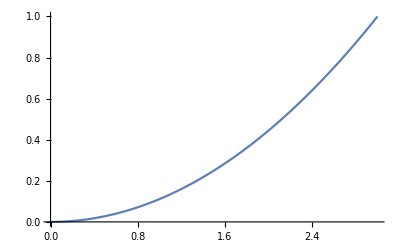

```mathematica
Plot[Pofr[r, 0, 3], {r, 0, 3}]
```

```mathematica
Integrate[Pofr[r, 0, 250], {r,0,250}]
```

1

## Define the integrals

### CMZ

```mathematica
NCMZ=3*10^5
```

300000

```mathematica
Clear[fcold]
```

```mathematica
fcold[nc_]:=0.7*150/nc
```

```mathematica
fwarm=0.3*150/10^2.5
```

0.142302

```mathematica
NcloudsCMZ1=NCMZ*fcold[10^3.5]
NcloudsCMZ2=NCMZ*fwarm
```

9961.17

42690.7

```mathematica
csCMZ=1;
csin1=10;
csin2=30;
```

1

10

30

```mathematica
mulowCMZ= Sqrt[130^2+50^2];
mumedCMZ= Sqrt[130^2+75^2];
muhighCMZ= Sqrt[130^2+100^2;]
```

10 √194

5 √901

10 √269

```mathematica
N[muhighCMZ]
```

164.012

```mathematica
N[mulowCMZ]
```

139.284

```mathematica
NIntegrate[Boole[-Tan[.35 Degree]<y/x< Tan[.35 Degree]],{x,y}∈Circle[{8000, 0}, 160]]/NIntegrate[1,{x,y}∈Circle[{0,0}, 160]]
```

0.197601

```mathematica
rwindow=NIntegrate[Boole[-Tan[.35 Degree]<y/x< Tan[.35 Degree]],{x,y, z}∈Cylinder[{{8300, 0, -15},{8300, 0, 15}}, 160]]/NIntegrate[1,{x,y, z}∈Cylinder[{{8300, 0, -15},{8300, 0, 15}}, 160]]
```

0.396612

```mathematica
NwindowCMZ=NCMZ*rwindow
```

118984.

```mathematica
NSourcesCMZBondi= Function[{N, mu, lambda, ncold}, N*fcold[ncold]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[FxBondi[v, ncold, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}] +
N*fwarm*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[FxBondi[v, 10^2.5, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}]];
```

```mathematica
NSourcesCMZRicotti= Function[{N, mu, lambda, csin,ncold, k}, N*fcold[ncold]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[Flux[v, ncold, m*Msun, 8.3*kpc, csCMZ, csin, k]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10] +
N*fwarm*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[Flux[v, 10^2.5, m*Msun, 8.3*kpc, csCMZ, csin, k]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10]];
```

```mathematica
NSourcesCMZRicotti[NwindowCMZ, muhighCMZ, 1 , csin1, 10^3.5, 0.3]
NSourcesCMZRicotti[NwindowCMZ, muhighCMZ, 1 , csin2, 10^3.5, 0.3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

188.626

162.938

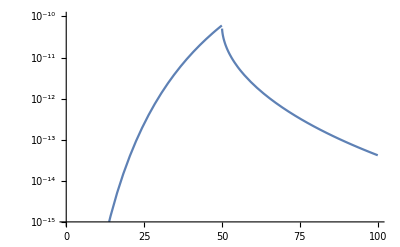

```mathematica
LogPlot[Flux[v, 10^4, 10*Msun, 8.3*kpc]/(erg/cm^2),{v, 0, 100}, PlotRange->{Automatic, {10^-15, 10^-10}}]
```

```mathematica
NSourcesRadioCMZRicottiSKA= Function[{N, mu, lambda, csin,ncold,nwarm, k}, N*fcold[ncold]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, ncold, m*Msun, 8.3*kpc, csCMZ, csin, k]> SKAsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->20] +
N*fwarm*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, nwarm, m*Msun, 8.3*kpc, csCMZ, csin, k]> SKAsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->20]];

NSourcesRadioCMZRicottiVLA= Function[{N, mu, lambda, csin,ncold,nwarm, k}, N*fcold[ncold]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, ncold, m*Msun, 8.3*kpc, csCMZ, csin, k]> VLAbound], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10] +
N*fwarm*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, nwarm, m*Msun, 8.3*kpc, csCMZ, csin, k]> VLAbound], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10]];
```

```mathematica
NSourcesRadioCMZRicottiSKA[10^4, 100, 1, 25, 10^4,10^2.5, .3]
NSourcesRadioCMZRicottiVLA[10^4, 100, 1, 25, 10^4,10^2.5, .3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

99% of BHs in dense molecular clouds would be detected by SKA:

```mathematica
NIntegrate[Pofv[v, 100]*PofM[m]*Boole[RFlux[v, 10^4, m*Msun, 8.3*kpc]> SKAsensitivity],{v, 1, 400}, {m, 1,100},  AccuracyGoal->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.99799

Also half of the BH in the warm clouds would emit above threshold.

```mathematica
NIntegrate[Pofv[v, 100]*PofM[m]*Boole[RFlux[v, 10^2.5, m*Msun, 8.3*kpc]> SKAsensitivity],{v, 1, 400}, {m, 1,100},  AccuracyGoal->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.467815 and 0.0000384468 for the integral and error estimates.

0.467815

These make up most of the visible sources since the filling factor is bigger:

```mathematica
10^4*fwarm
```

1423.02

```mathematica
10^4*fwarm*0.46
```

654.591

We must therefore take into account also the dependence on the density of these warm clouds.

```mathematica
10^4*fwarm*NIntegrate[Pofv[v, 100]*PofM[m]*Boole[RFlux[v, 10^3, m*Msun, 8.3*kpc]> SKAsensitivity],{v, 1, 400}, {m, 1,100},  AccuracyGoal->20] 
10^4*fwarm*NIntegrate[Pofv[v, 100]*PofM[m]*Boole[RFlux[v, 10^2, m*Msun, 8.3*kpc]> SKAsensitivity],{v, 1, 400}, {m, 1,100},  AccuracyGoal->20]
```

### Fender Setup

```mathematica
NcloudsNear1=175;
NcloudsNear2=1750;
cs1Fender=.6;
cs2Fender=.9;
muNoKickFender=25;
muHighKickFender=75;
```

Bondi scenario. Fender finds max lambda=0.01 for the no kick scenario. For this lambda no sources in the high kick scenario.

```mathematica
lambdaFender=0.01;
```

```mathematica
NSourcesNearBondi= Function[{lambda, mu},NcloudsNear1*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[FxBondi[v, 10^3, m*Msun, r*kpc, cs1Fender]/(erg/cm^2)> FenderBound], {v, 1, 400}, {m, 1,100}, {r, 0.07, 0.250}] +
NcloudsNear2*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[FxBondi[v, 10^2, m*Msun, r*kpc, cs2Fender]/(erg/cm^2)> FenderBound], {v, 1, 400}, {m, 1,100}, {r, 0.07, 0.250}]];
```

```mathematica
NSourcesNearRicotti= Function[{lambda, mu, csin},NcloudsNear1*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[Flux[v, 10^3, m*Msun, r*kpc, cs1Fender, csin]/(erg/cm^2)> FenderBound], {v, 0, Infinity}, {m, 0,Infinity}, {r, 0.07, 0.250}] +
NcloudsNear2*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[Flux[v, 10^2, m*Msun, r*kpc, cs2Fender, csin]/(erg/cm^2)> FenderBound], {v, 0, Infinity}, {m, 0,Infinity}, {r, 0.07, 0.250}]];
```

```mathematica
NSourcesNearBondi[0.01, muNoKickFender]
```

11.384

```mathematica
NSourcesNearRicotti[1, muHighKickFender, csin1]
NSourcesNearRicotti[1, muHighKickFender, csin2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.309293 and 0.0015747 for the integral and error estimates.

103.243

45.3076

## Plot the expected value for N Xray

```mathematica
labelN=DisplayForm[StyleBox["Number of Xray sources",FontSize->25]];
labelLambda=DisplayForm[StyleBox["λ",FontSize->25]];
```

```mathematica
labelBondiNo=DisplayForm[StyleBox["Bondi, no kick",FontSize->15]];
labelBondiLow=DisplayForm[StyleBox["Bondi, low kick",FontSize->15]];
labelBondiHigh=DisplayForm[StyleBox["Bondi, high kick",FontSize->15]];
labelRicottiNo=DisplayForm[StyleBox["Ricotti, no kick",FontSize->15]];
labelRicottiLow=DisplayForm[StyleBox["Ricotti, low kick",FontSize->15]];
labelRicottiHigh=DisplayForm[StyleBox["Ricotti, high kick",FontSize->15]];
```

Nustar Bound

```mathematica
fticksN= Table[If[IntegerQ[i/100],{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,0,500,10}];
fticksLambda= Table[{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{i,0,1,0.1}];
```

```mathematica
NearTitle=DisplayForm[StyleBox["Nearest 250 pc ",FontSize->30]];
```

### Fender Bound

```mathematica
Legended[
Plot[{NSourcesNearBondi[lambda, muNoKickFender], 
NSourcesNearBondi[lambda, muHighKickFender],  
NSourcesNearRicotti[1, muNoKickFender, 25], 
NSourcesNearRicotti[1, muHighKickFender,25],
100},
 {lambda, 10^-3, 1},
Frame->True,
PlotLabel->NearTitle,
FrameLabel->{labelLambda,labelN}, 
FrameTicks->{{fticksN, None},{fticksLambda, None}},
ImageSize->800,
PlotLabels->{labelBondiNo,labelBondiHigh, labelRicottiNo,labelRicottiHigh, None}, 
PlotStyle->{Automatic, Automatic, Thick, Thick, Dashed}, 
PlotLabel->"Nuber of X-ray Sources",
PlotRange->{{0,1}, {0,500}
} 
],
None
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in v near {v,m,r} = {1.,0.184661,0.221942}. NIntegrate obtained 0. and 0. for the integral and error estimates.

Velocity dependence in the two descriptions

```mathematica
labelBondi1=DisplayForm[StyleBox["Bondi, λ=1",FontSize->15]];
labelBondi001=DisplayForm[StyleBox["Bondi, λ=0.01",FontSize->15]];
labelRicotti=DisplayForm[StyleBox["Ricotti",FontSize->15]];
```

```mathematica
Legended[
Plot[{NSourcesNearBondi[1, mu],
NSourcesNearBondi[0.01, mu],
NSourcesNearRicotti[1, mu, 25],
100},
 {mu, 5, 200},
Frame->True,
PlotLabel->NearTitle,
FrameLabel->{labelv,labelN}, 
FrameTicks->{{fticksN, None},{fticksD, None}},
ImageSize->800,
PlotLabels->{labelBondi1,labelBondi001, labelRicotti, None}, 
PlotStyle->{Automatic, Automatic, Thick, Dashed}, 
PlotLabel->"Nuber of X-ray Sources",
PlotRange->{{0,200}, {0,300}
} 
],
None
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in v near {v,m,r} = {1.,0.184661,0.221942}. NIntegrate obtained 0. and 0. for the integral and error estimates.

-Graphics-

### Central Molecular Zone

```mathematica
CMZtitle=DisplayForm[StyleBox["Central Molecular Zone ",FontSize->30]];
```

```mathematica
Legended[
Plot[{NSourcesCMZBondi[NwindowCMZ, mulowCMZ, lambda, 10^3.5], 
NSourcesCMZBondi[NwindowCMZ,  muhighCMZ, lambda, 10^3.5], 
NSourcesCMZRicotti[NwindowCMZ, mulowCMZ, 1, 25, 10^3.5, 0.3], 
NSourcesCMZRicotti[NwindowCMZ, muhighCMZ, 1, 25, 10^3.5, 0.3],
20},
 {lambda, 10^-3, 1},
Frame->True,
PlotLabel->CMZtitle,
FrameLabel->{labelLambda,labelN}, 
FrameTicks->{{fticksN, None},{fticksLambda, None}},
ImageSize->800,
PlotLabels->{labelBondiLow,labelBondiHigh, labelRicottiLow,labelRicottiHigh, labelNustarBound}, 
PlotStyle->{Automatic, Automatic, Thick, Thick, Dashed}, 
PlotLabel->"Nuber of X-ray Sources",
PlotRange->{{0,1}, {0,300}
} 
],
None
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

```mathematica
fticksNlog2=Table[Which[IntegerQ[Log[10,i]], {i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},
IntegerQ[i/1000],{i,"",{.018,0},Black},
True,{i,"",{.007,0},Black}],{i, Flatten[Table[10^j*k,{j,1,4},{k,1,9}]]}];
```

```mathematica
Legended[
LogPlot[{NSourcesCMZBondi[NwindowCMZ, mu, 1, 10^3.5],
NSourcesCMZBondi[NwindowCMZ, mu, 0.01, 10^3.5],
NSourcesCMZRicotti[NwindowCMZ, mu, 1, 25, 10^3.5, 0.3],
20},
 {mu, 5, 300},
Frame->True,
PlotLabel->CMZtitle,
FrameLabel->{labelavv,labelN}, 
FrameTicks->{{fticksNlog2, None},{fticksD, None}},
ImageSize->800,
PlotLabels->{labelBondi1,labelBondi001, labelRicotti, labelNustarBound}, 
PlotStyle->{Automatic, Automatic, Thick, Dashed}, 
PlotLabel->"Nuber of X-ray Sources",
PlotRange->{{0,300}, {1,30000}} 
],
None
]
```

-Graphics-

```mathematica
labelNustarBound=DisplayForm[StyleBox["Nustar Bound",FontSize->15]];
labelNtot=DisplayForm[StyleBox["Number of BHs in the Galaxy",FontSize->30]];
CMZtitlecont=DisplayForm[StyleBox["CMZ Nustar Bound ",FontSize->30]];
```

```mathematica
fticksNlog=Table[Which[IntegerQ[Log[10,i]],{i,DisplayForm[StyleBox[SuperscriptBox["10",Log[10,i]],FontSize->20]],{.018,0},Black},
IntegerQ[Log[10,i]],{i,,{.018,0},Black},
True,{i,"",{.007,0},Black}],{i,Flatten[Table[10^j*k,{j,0,10},{k,1,9}]]}];
```

### CMZ, as a function of the luminosity fraction in Xrays

```mathematica
Legended[
LogPlot[{
NSourcesCMZRicotti[NwindowCMZ, 150, 1, 25, 10^4, k],
NSourcesCMZRicotti[NwindowCMZ, 150, 1, 25, 10^3.5, k],
NSourcesCMZRicotti[NwindowCMZ, 150, 1, 25, 10^3, k],
70,
10

},
{k, 0, 1},
Frame->True,
FrameLabel->{labelfl,labelN}, 
FrameTicks->{{fticksNlog2, None},{fticksLambda, None}},
ImageSize->800,
PlotStyle->{{Red, Opacity[.5], Dotted, Thick},{Red, Opacity[.5], Dashed, Thick}, {Red, Opacity[.5], Thick}, {Darker[Red], Opacity[.3], Dashed, Thin}, {Darker[Red], Opacity[.3], Dashed, Thin}},
PlotRange->{{0,1}, {1,30000}} 
],
{Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 25  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 150  km/s"}],FontSize->15]],  {.85,.09}],
Placed[Framed[linelegendn,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.75}]}
]
```

## Nustar bound on the Number of BHs

### Total BHs in the galaxy

Define a function to compute the bound:

```mathematica
NsolveRicotti=Function[{mu, csin, ncold, k},NSolve[NSourcesCMZRicotti[N.15*.02,mu,1, csin, ncold, k]== 10 && N>0 , N , Reals]];
NBoundNustarRicotti=Function[{mu, csin, ncold, k}, N/.NsolveRicotti[mu, csin, ncold, k]];
```

```mathematica
NsolveRicotti[150,10, 10^3.5, 0.2]
```

{{N→1.93543×10^6}}

```mathematica
NsolveBondi=Function[{mu, lambda, ncold},NSolve[NSourcesCMZBondi[N.15*.02,mu,lambda, ncold]== 10 && N>0 , N , Reals]];
NBoundNustarBondi=Function[{mu, lambda, ncold}, N/.NsolveBondi[mu, lambda, ncold]];
```

```mathematica
NBoundNustarRicotti[150,10, 10^3.5, 0.2]
NBoundNustarRicotti[150,30, 10^3.5, 0.2]
```

{1.93543×10^6}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{2.37973×10^6}

Draw the plots:

```mathematica
linelegend=LineLegend[{Directive[Red, Opacity[.5]],Directive[Blue, Opacity[.5]],Directive[Blue, Opacity[.5], Dashed]},{labelRicotti,labelBondi001,labelBondi1}];
```

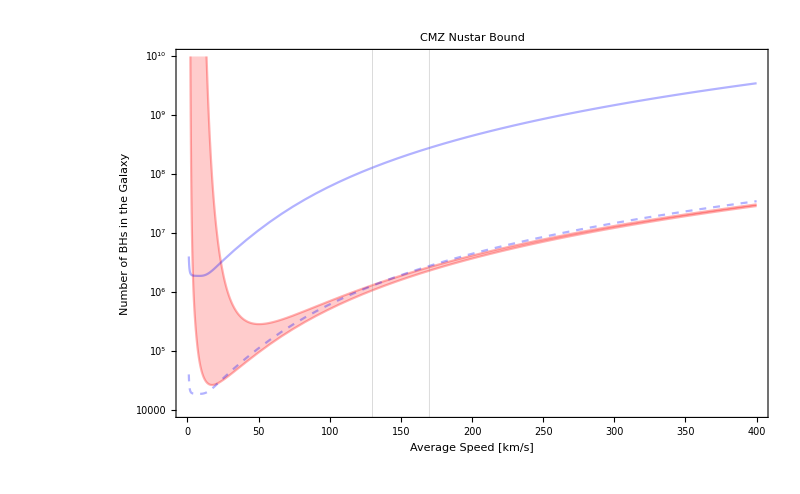

```mathematica
Legended[
Plot[
{NBoundNustarRicotti[mu, 10, 10^3.5, 0.3],
NBoundNustarRicotti[mu, 30, 10^3.5, 0.3],
NBoundNustarBondi[mu,0.01, 10^3.5],
NBoundNustarBondi[mu, 1, 10^3.5]
},
{mu, 1, 400},
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelavv,labelNtot}, 
FrameTicks->{{fticksNlog, None},{fticksD, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],{{Blue, Opacity[.3]}}, {{Blue, Opacity[.3], Dashed}}],
Filling->{1->{2}},
ScalingFunctions->{None,"Log"},
PlotRange->{{0,400}, {10^4, 10^10}} ,
GridLines->{{130, 170}, None}
], 

 Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]
]
```

### N of BHs in the CMZ clouds

Now define the same function but for the number of BH in the CMZ clouds

Our best guess based on the literature is

```mathematica
NCMZ
NwindowCMZ
rwindow
fcold
```

300000

118984.

0.396612

0.0332039

```mathematica
NCMZ*fcold
```

9961.17

```mathematica
NwindowCMZ*fcold
```

3950.72

```mathematica
NcloudsCMZ1*rwindow/fcold
```

118984.

9961.17

The following gives us the total number of BH in the cmz window that corresponds to the nustar bound. (The name is misleading! To get the n of BHs in the clouds we must divide by rwindow and multiply by fclouds)

```mathematica
NCloudssolveRicotti=Function[{mu, csin, ncold, k},NSolve[NSourcesCMZRicotti[N,mu,1, csin, ncold, k]== 10 && N>0 , N , Reals]];
NCloudsBoundNustarRicotti=Function[{mu, csin, ncold, k}, N/.NCloudssolveRicotti[mu, csin, ncold, k]];
```

```mathematica
NCloudssolveBondi=Function[{mu, lambda, ncold, k},NSolve[NSourcesCMZBondi[N,mu,lambda, ncold, k]== 10 && N>0 , N , Reals]];
NCloudsBoundNustarBondi=Function[{mu, lambda, ncold, k}, N/.NCloudssolveBondi[mu, lambda, ncold, k]];
```

```mathematica
labelNclouds2=DisplayForm[StyleBox["N of BHs in the dense clouds",FontSize->30]];
labelNclouds=DisplayForm[StyleBox["N of BHs in molecular clouds",FontSize->30]];
labelBestGuess=DisplayForm[StyleBox["Best guess",FontSize->15]];
```

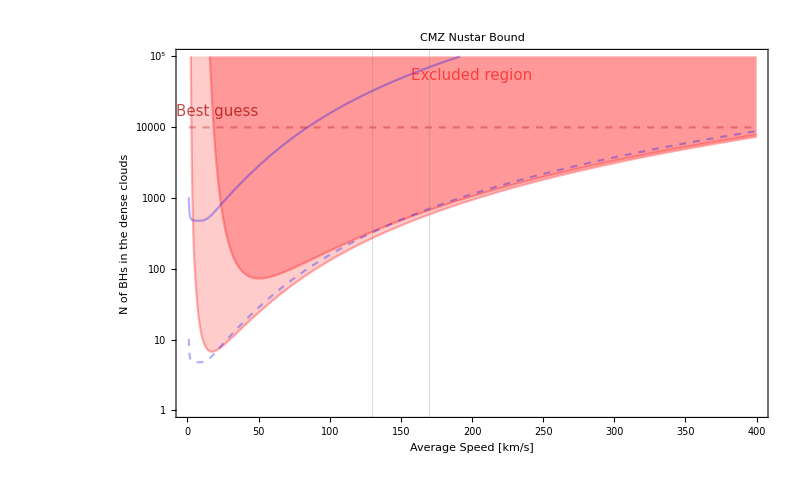

```mathematica
Legended[
Plot[
{NCloudsBoundNustarRicotti[mu, 10, 10^3.5, 0.3]/rwindow*fcold,
NCloudsBoundNustarRicotti[mu, 30,  10^3.5, 0.3]/rwindow*fcold,
NCloudsBoundNustarBondi[mu,0.01, 10^3.5, 0.3]/rwindow*fcold,
NCloudsBoundNustarBondi1[mu,1, 10^3.5, 0.3]/rwindow*fcold,
NcloudsCMZ1
},
{mu, 1, 400},
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelavv,labelNclouds2}, 
FrameTicks->{{fticksNlog, None},{fticksD, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],{{Blue, Opacity[.3]}}, {{Blue, Opacity[.3], Dashed}}, {{Darker[Red], Opacity[.3], Dashed}}],
Filling->{{2-> {Top,Directive[Red, Opacity[.4]]}},{1->{{2},Directive[Red, Opacity[.2]]}} },
ScalingFunctions->{None,"Log"},
PlotRange->{{0,400}, {10^0, 10^5}} ,
GridLines->{{130, 170}, None}
], 

 {Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.35}],
Placed [DisplayForm[StyleBox["Best guess",FontSize->15, Darker[Red], Opacity[.7]]], {.07,.83}],
Placed [DisplayForm[StyleBox["Excluded region",FontSize->15, Red, Opacity[.6]]], {.5,.93}]}
]
```

```mathematica
NCloudsBoundNustarRicotti
```

Function[{mu,csin,ncold},N/.NCloudssolveRicotti[mu,csin,ncold]]

```mathematica
NCloudsBoundNustarRicotti[170, 30,  10^3.5]/rwindow*fcold[10^3.5]
```

{673.614}

### Bound on total number as a function of n_cold

```mathematica
labelRicotti10=DisplayForm[StyleBox[RowBox[{"Ricotti, ", SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 10  km/s"}],FontSize->15]]
labelRicotti25=DisplayForm[StyleBox[RowBox[{"Ricotti, ", SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 25  km/s"}],FontSize->15]]
labelRicotti50=DisplayForm[StyleBox[RowBox[{"Ricotti, ", SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 50  km/s"}],FontSize->15]]
```

Ricotti, c_s^in= 10  km/s

Ricotti, c_s^in= 25  km/s

Ricotti, c_s^in= 50  km/s

```mathematica
linelegendcs=LineLegend[{Directive[Red, Opacity[.5]],Directive[Blue, Opacity[.5]], Directive[Gray, Opacity[.5]]},{labelRicotti10,labelRicotti25,labelRicotti50}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

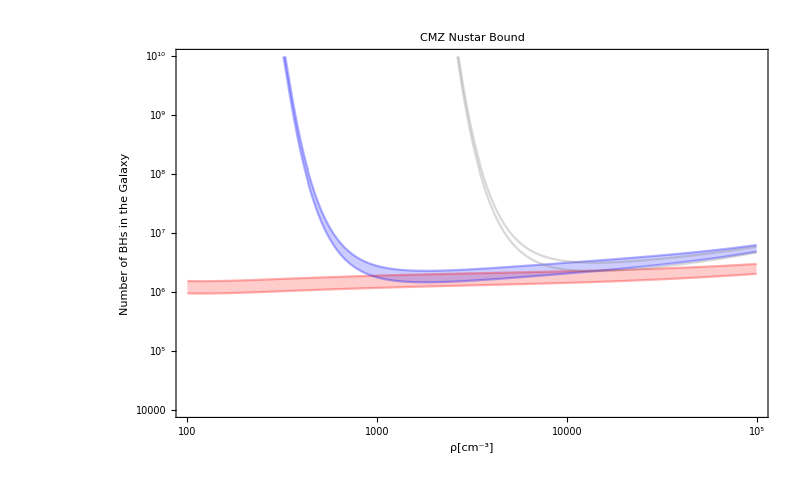

```mathematica
Legended[
LogLogPlot[
{NBoundNustarRicotti[mulowCMZ, 10, n, 0.3],
NBoundNustarRicotti[muhighCMZ, 10, n, 0.3],
NBoundNustarRicotti[mulowCMZ, 25, n, 0.3],
NBoundNustarRicotti[muhighCMZ, 25, n, 0.3],
NBoundNustarRicotti[mulowCMZ, 50, n, 0.3],
NBoundNustarRicotti[muhighCMZ, 50, n, 0.3]
},
{n, 10^2, 10^5},
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelrho,labelNtot}, 
FrameTicks->{{fticksNlog, None},{fticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],Table[{Blue, Opacity[.3]}, {i,2}], Table[{Gray, Opacity[.3]}, {i,2}]],
Filling->{1->{2}, 3->{4}},
PlotRange->{{10^2,10^5}, {10^4, 10^10}} ,
GridLines->{{10^3.5, 10^4}, None}
], 

 Placed[Framed[linelegendcs,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]
]
```

### Dependence on the luminosity factor k

```mathematica
labelfl=DisplayForm[StyleBox[SubscriptBox["f", "L"],FontSize->30]];
```

f_L

```mathematica
labeln3=DisplayForm[StyleBox[RowBox[{"n = ", SuperscriptBox["10", "3"],SuperscriptBox["cm", "-3"]}],FontSize->15]]
labeln35=DisplayForm[StyleBox[RowBox[{"n = ", SuperscriptBox["10", "3.5"],SuperscriptBox["cm", "-3"]}],FontSize->15]]
labeln4=DisplayForm[StyleBox[RowBox[{"n = ", SuperscriptBox["10", "4"],SuperscriptBox["cm", "-3"]}],FontSize->15]]
```

```mathematica
linelegendn=LineLegend[{Directive[Red, Opacity[.5]],Directive[Red, Opacity[.5], Dashed],Directive[Red, Opacity[.5], Dotted]},{labeln3,labeln35,labeln4}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

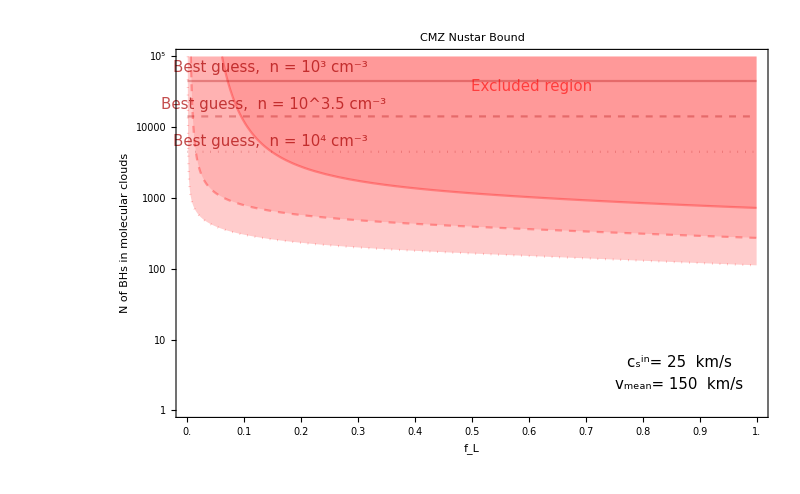

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

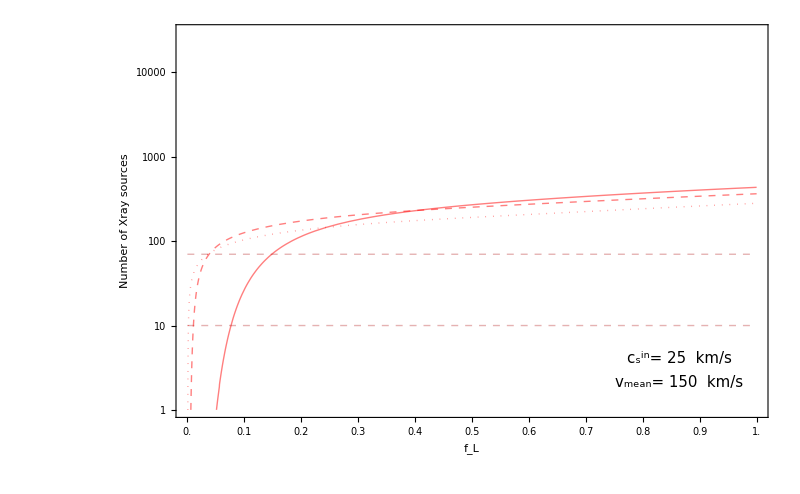

```mathematica
Legended[
Plot[
{NCloudsBoundNustarRicotti[150, 25, 10^4, k]/rwindow*fcold[10^4],
NCloudsBoundNustarRicotti[150, 25, 10^3.5, k]/rwindow*fcold[10^3.5],
NCloudsBoundNustarRicotti[150, 25,  10^3, k]/rwindow*fcold[10^3],

NCMZ*fclouds[10^4],
NCMZ*fclouds[ 10^3.5],
NCMZ*fclouds[10^3]
},
{k, 0, 1},
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelfl,labelNclouds}, 
FrameTicks->{{fticksNlog, None},{fticksLambda, None}},
ImageSize->800 ,
PlotStyle->{{Red, Opacity[.3], Dotted},{Red, Opacity[.3], Dashed}, {Red, Opacity[.3]}, {Darker[Red], Opacity[.3],  Dotted}, {Darker[Red], Opacity[.3], Dashed}, {Darker[Red], Opacity[.3]}},
Filling->{{3-> {Top,Directive[Red, Opacity[.4]]}},{1->{{2},Directive[Red, Opacity[.2]]}} , {2->{{3},Directive[Red, Opacity[.3]]}}},
ScalingFunctions->{None,"Log"},
PlotRange->{{0,1}, {10^0, 10^5}} 
], 


{Placed [DisplayForm[StyleBox[RowBox[{"Best guess, " "n = ", SuperscriptBox["10", "3"],SuperscriptBox["cm", "-3"]}],FontSize->15, Darker[Red], Opacity[.7]]], {.16,.95}],
Placed [DisplayForm[StyleBox[RowBox[{"Best guess, " "n = ", SuperscriptBox["10", "3.5"],SuperscriptBox["cm", "-3"]}],FontSize->15, Darker[Red], Opacity[.7]]], {.165,.85}],
Placed [DisplayForm[StyleBox[RowBox[{"Best guess, " "n = ", SuperscriptBox["10", "4"],SuperscriptBox["cm", "-3"]}],FontSize->15, Darker[Red], Opacity[.7]]], {.16,.75}],
Placed [DisplayForm[StyleBox["Excluded region",FontSize->15, Red, Opacity[.6]]], {.6,.90}],
Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 25  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 150  km/s"}],FontSize->15]],  {.85,.09}],
Placed[Framed[linelegendn,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.75}]}
]
```

```mathematica
NCloudsBoundNustarRicotti[150, 10, 10^4, .3]/rwindow*fcold[10^4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
{141.12864591310299
```

```mathematica
fcold[10^4]
```

0.0105

## Try different prescriptions for the gas density

### 1. Only one type of clouds

```mathematica
fclouds[nc_]:=150/nc
```

```mathematica
NSourcesCMZBondi1= Function[{N, mu, lambda, nclouds}, N*fclouds[nclouds]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[FxBondi[v, nclouds, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}]] ;
NSourcesCMZRicotti1= Function[{N, mu, lambda, csin,nclouds, k}, N*fclouds[nclouds]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[Flux[v, nclouds, m*Msun, 8.3*kpc, csCMZ, csin, k]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10]] ;
```

```mathematica
NsolveRicotti1=Function[{mu, csin, nclouds, k},NSolve[NSourcesCMZRicotti1[N.15*.02,mu,1, csin,nclouds, k]== 10 && N>0 , N , Reals]];
NBoundNustarRicotti1=Function[{mu, csin, nclouds, k}, N/.NsolveRicotti1[mu, csin, nclouds, k]];

NsolveBondi1=Function[{mu, lambda, nclouds},NSolve[NSourcesCMZBondi1[N.15*.02,mu,lambda, nclouds]== 10 && N>0 , N , Reals]];
NBoundNustarBondi1=Function[{mu, lambda, nclouds}, N/.NsolveBondi1[mu, lambda,nclouds]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

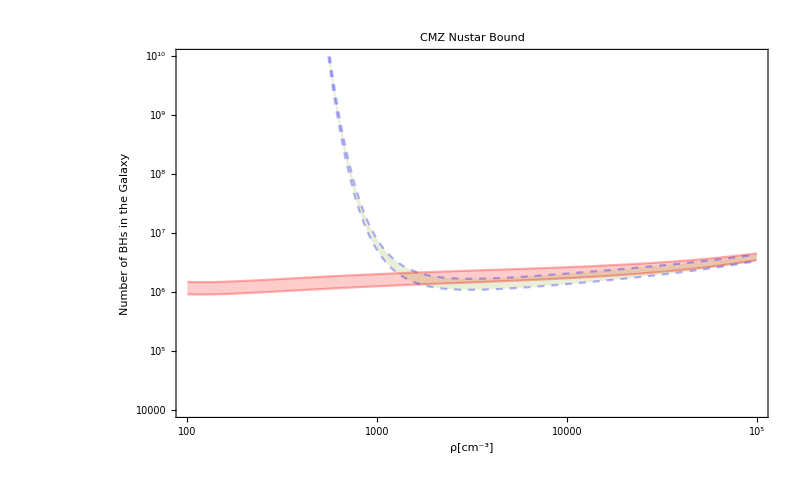

```mathematica
Legended[
LogLogPlot[
{NBoundNustarRicotti1[mulowCMZ, 10, n, 0.3],
NBoundNustarRicotti1[muhighCMZ, 10, n, 0.3],
NBoundNustarRicotti1[mulowCMZ, 25, n, 0.3],
NBoundNustarRicotti1[muhighCMZ, 25, n, 0.3],
NBoundNustarRicotti1[mulowCMZ, 50, n, 0.3],
NBoundNustarRicotti1[muhighCMZ, 50, n, 0.3],
10^8
},
{n, 10^2, 10^5},
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelrho,labelNtot}, 
FrameTicks->{{fticksNlog, None},{fticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],Table[{Blue, Opacity[.3]}, {i,2}], Table[{Gray, Opacity[.3]}, {i,2}]],
Filling->{1->{2}, 3->{4}},
PlotRange->{{10^2,10^5}, {10^4, 10^10}} ,
GridLines->{{10^3.5, 10^4}, None}
], 

 Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]
]
```

```mathematica
NCloudssolveRicotti1=Function[{mu, csin, nclouds, k},NSolve[NSourcesCMZRicotti1[N,mu,1, csin, nclouds, k]== 10 && N>0 , N , Reals]];
NCloudsBoundNustarRicotti1=Function[{mu, csin, nclouds, k}, N/.NCloudssolveRicotti1[mu, csin, nclouds, k]];

NCloudssolveBondi1=Function[{mu, lambda, nclouds},NSolve[NSourcesCMZBondi1[N,mu,lambda, nclouds]== 10 && N>0 , N , Reals]];
NCloudsBoundNustarBondi1=Function[{mu, lambda, nclouds}, N/.NCloudssolveBondi1[mu, lambda, nclouds]];
```

```mathematica
Legended[
LogLogPlot[
{NCloudsBoundNustarRicotti1[mulowCMZ, 10, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[muhighCMZ, 10, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[mulowCMZ, 25, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[muhighCMZ, 25, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[mulowCMZ, 50, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[muhighCMZ, 50, n]/rwindow*fclouds[n],
NCMZ*fclouds[n]
},
{n, 10^2, 10^5},
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelrho,labelNclouds}, 
FrameTicks->{{fticksNlog, None},{fticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],Table[{Blue, Opacity[.3]}, {i,2}], Table[{Gray, Opacity[.3]}, {i,2}], {{Darker[Red], Opacity[.3], Dashed}}],
Filling->{1->{2}, 3->{4}, 5->{6}},

PlotRange->{{10^2,10^5}, {10, 10^6}} ,
GridLines->{{10^3.5, 10^4}, None}
], 

 {Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}],
Placed [DisplayForm[StyleBox["Best guess",FontSize->15, Darker[Red], Opacity[.7]]], {.07,.83}]}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

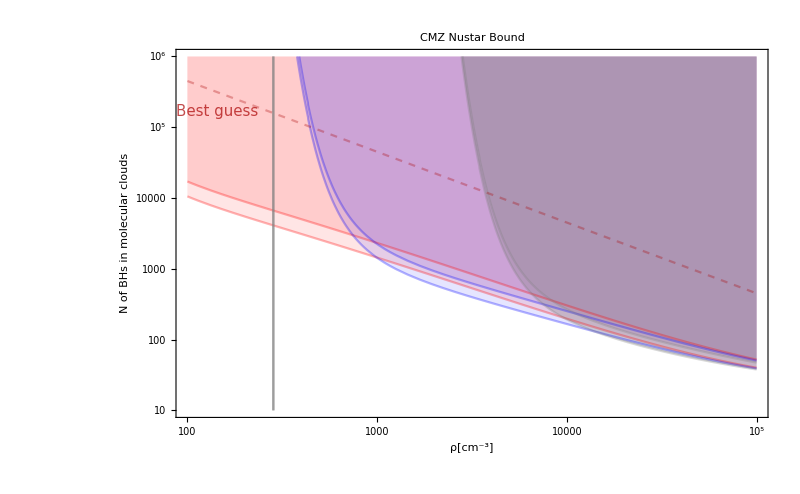

```mathematica
Legended[
LogLogPlot[
{NCloudsBoundNustarRicotti1[mulowCMZ, 10, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[muhighCMZ, 10, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[mulowCMZ, 25, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[muhighCMZ, 25, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[mulowCMZ, 50, n]/rwindow*fclouds[n],
NCloudsBoundNustarRicotti1[muhighCMZ, 50, n]/rwindow*fclouds[n],

NCMZ*fclouds[n]
},
{n, 10^2, 10^5},
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelrho,labelNclouds}, 
FrameTicks->{{fticksNlog, None},{fticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],Table[{Blue, Opacity[.3]}, {i,2}], Table[{Gray, Opacity[.3]}, {i,2}], {{Darker[Red], Opacity[.3], Dashed}}],

Filling->{{2-> {Top,Directive[Red, Opacity[.2]]}},{1->{{2},Directive[Red, Opacity[.1]]}} ,
{4-> {Top,Directive[Blue, Opacity[.2]]}},{3->{{4},Directive[Blue, Opacity[.1]]}},
{6-> {Top,Directive[Gray, Opacity[.4]]}},{5->{{6},Directive[Gray, Opacity[.3]]}}},


PlotRange->{{10^2,10^5}, {10, 10^6}} ,
GridLines->{{10^3.5, 10^4}, None}
], 

 {Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}],
Placed [DisplayForm[StyleBox["Best guess",FontSize->15, Darker[Red], Opacity[.7]]], {.07,.83}]}
]
```

### 2. Introduce parameter r_dense

```mathematica
ndense=10^3.5
```

3162.28

```mathematica
fdense[rdense_]:=150*rdense/ndense
```

```mathematica
NSourcesCMZBondiR= Function[{N, mu, lambda, rdense}, N*fdense[rdense]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[FxBondi[v, ndense, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}]] ;
NSourcesCMZRicottiR= Function[{N, mu, lambda, csin,nclouds}, N*fdense[rdense]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[Flux[v, ndense, m*Msun, 8.3*kpc, csCMZ, csin]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10]] ;
```

```mathematica
NsolveRicottiR=Function[{mu, csin, rdense},NSolve[NSourcesCMZRicottiR[N.15*.02,mu,1, csin,rdense]== 10 && N>0 , N , Reals]];
NBoundNustarRicottiR=Function[{mu, csin, rdense}, N/.NsolveRicottiR[mu, csin, rdense]];

NsolveBondiR=Function[{mu, lambda, rdense},NSolve[NSourcesCMZBondiR[N.15*.02,mu,lambda, rdense]== 10 && N>0 , N , Reals]];
NBoundNustarBondiR=Function[{mu, lambda,rdense}, N/.NsolveBondiR[mu, lambda,rdense]];
```

```mathematica
labelrdense=DisplayForm[RowBox[{StyleBox["Fraction of CMZ clouds with n = 10^3.5",FontSize->30],StyleBox[RowBox[{"[", SuperscriptBox["cm", "-3"], "]"}],FontSize->25]}]];
```

```mathematica
Legended[
Plot[
{NBoundNustarRicottiR[mulowCMZ, 10, rdense],
NBoundNustarRicottiR[muhighCMZ, 30, rdense],
NBoundNustarBondiR[mulowCMZ,1, rdense],
NBoundNustarBondiR[muhighCMZ, 1, rdense]
},
{rdense, 0, 1},
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelrho,labelNtot}, 
FrameTicks->{{fticksNlog, None},{fticksLambda, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],Table[{Blue, Opacity[.3], Dashed}, {i,2}]],
Filling->{1->{2}, 3->{4}},
PlotRange->{{0,1}, {10^4, 10^10}} ,
GridLines->{{10^3.5, 10^4}, None},
ScalingFunctions->{None,"Log"}
], 

 Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]
]
```

### 3. Power law

## Plot the expected N for SKA in the allowed region

### Bound on total BHs in the Galaxy

```mathematica
NsolveRicottiRadio=Function[{mu, csin, ncold, k},NSolve[NSourcesRadioCMZRicottiSKA[N.15*.02,mu,1, csin, ncold, k]== 10 && N>0 , N , Reals]]
```

Function[{mu,csin,ncold,k},NSolve[NSourcesRadioCMZRicottiSKA[N 0.15 0.02,mu,1,csin,ncold,k]==i&&N>0,N,Reals]]

```mathematica
NsolveRicottiRadio[150,25, 10^4, 0.3]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N→ConditionalExpression[1.06733×10^14 i,i>0]}}

```mathematica
NSourcesRadioCMZRicottiSKA[10^4, 150,1, 25, 10^4, 0.3]
```

3.12307×10^-8

```mathematica
NsolveRicottiRadio=Table[Function[{mu, csin, ncold, k},NSolve[NSourcesRadioCMZRicottiSKA[N.15*.02,mu,1, csin, ncold, k]== i && N>0 , N , Reals]], {i, {10, 100}}]
```

{Function[{mu,csin,ncold,k},NSolve[NSourcesRadioCMZRicottiSKA[N 0.15 0.02,mu,1,csin,ncold,k]==i&&N>0,N,Reals]],Function[{mu,csin,ncold,k},NSolve[NSourcesRadioCMZRicottiSKA[N 0.15 0.02,mu,1,csin,ncold,k]==i&&N>0,N,Reals]]}

```mathematica
NsolveRicottiRadio[[1]][150,25, 10^4, 0.3]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N→ConditionalExpression[1.06733×10^14 i,i>0]}}

```mathematica
NSKARicotti=Table[Function[{mu, csin, ncold, k}, N/.NsolveRicottiRadio[mu, csin, ncold, k]]
```

Function[{mu,csin,ncold,k},N/.NsolveRicottiRadio[mu,csin,ncold,k]]

```mathematica
NSKARicotti[150,25, 10^4, 0.3]
```

ReplaceAll::reps: {{Function[{mu,csin,ncold,k},NSolve[NSourcesRadioCMZRicottiSKA[Times[«3»],mu,1,csin,ncold,k]==i&&N>0,N,Reals]],Function[{mu,csin,ncold,k},NSolve[NSourcesRadioCMZRicottiSKA[Times[«3»],mu,1,csin,ncold,k]==i&&N>0,N,Reals]]}[150,25,10000,0.3]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

N/.{Function[{mu,csin,ncold,k},NSolve[NSourcesRadioCMZRicottiSKA[N 0.15 0.02,mu,1,csin,ncold,k]==i&&N>0,N,Reals]],Function[{mu,csin,ncold,k},NSolve[NSourcesRadioCMZRicottiSKA[N 0.15 0.02,mu,1,csin,ncold,k]==i&&N>0,N,Reals]]}[150,25,10000,0.3]

### Bound on BHs in the clouds

### Bound on lambda

## Apply the model to PBHs

```mathematica
Rs=16 kpc
Mbulge=0.4*1.84*10^10*Msun
Rbulge=2*kpc
rho0=Mbulge/(4*Pi*Rs^3*(Log[(Rs+Rbulge)/Rs]- Rbulge/(Rs+Rbulge)))
```

4.9376×10^20

1.46349×10^40

6.172×10^19

1.45004×10^-21

```mathematica
rhoNFW[r_]:=1/(r/Rs(1+r/Rs)^2)
```

```mathematica
Plot[rho0*rhoNFW[r], {r, 0, 10kpc}]
```

-Graphics-

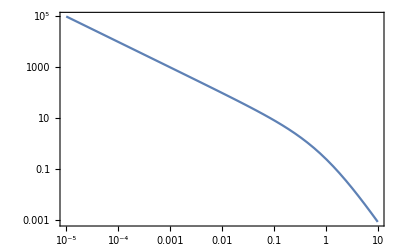

```mathematica
LogLogPlot[rhoNFW[r*Rs], {r, 10^-5,10^1}, Frame->True]
```

```mathematica
NIntegrate[rho0*rhoNFW[r]*r^2*4*Pi, {r, 0, Rbulge}]/Msun
```

7.36×10^9

```mathematica
DMMassCMZ=NIntegrate[rho0*2 Pi R*rhoNFW[Sqrt[R^2+z^2]], {R, 0, 0.16*kpc}, {z, -0.015*kpc, 0.015*kpc}]/Msun;
```

```mathematica
sigmamassPBH=10;
mumassPBH= 30;
```

```mathematica
NPBHCMZ=DMMassCMZ/mumassPBH
```

325660.

```mathematica
muvelPBH= Sqrt[8/Pi]*35
N[muvelPBH]
```

70 √(2/π)

55.8519

```mathematica
Clear[NPBHCMZRicotti1]
Clear[NsolveRicotti1PBH]
Clear[NBoundNustarRicotti1PBH]
```

### With gaussian mass function:

```mathematica
NPBHCMZBondi1= Function[{N, mu, lambda, nclouds}, N*fclouds[nclouds]*lambda*NIntegrate[Pofv[v, mu]*PofM[m, mumassPBH, sigmamassPBH ]*Boole[FxBondi[v, nclouds, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}]] ;
NPBHCMZRicotti1= Function[{N, mu, lambda, csin,nclouds, k, mumassPBH}, N*fclouds[nclouds]*lambda*NIntegrate[Pofv[v, mu]*PofM[m, mumassPBH, sigmamassPBH ]*Boole[Flux[v, nclouds, m*Msun, 8.3*kpc, csCMZ, csin,k]/(erg/cm^2)> NustarBound], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10]] ;
```

```mathematica
NsolveRicotti1PBH=Function[{mu, csin, nclouds, k, mumassPBH},NSolve[NPBHCMZRicotti1[N,mu,1, csin,nclouds, k, mumassPBH]*rwindow== 10 && N>0 , N , Reals]];
NBoundNustarRicotti1PBH=Function[{mu, csin, nclouds, k, mumassPBH}, N/.NsolveRicotti1PBH[mu, csin, nclouds, k, mumassPBH]];

NsolveBondi1PBH=Function[{mu, lambda, nclouds},NSolve[NPBHCMZBondi1[N,mu,lambda, nclouds]*rwindow== 10 && N>0 , N , Reals]];
NBoundNustarBondi1PBH=Function[{mu, lambda, nclouds}, N/.NsolveBondi1PBH[mu, lambda,nclouds]];
```

```mathematica
fticksfDM=Table[Which[IntegerQ[Log[10,i]],{i,DisplayForm[StyleBox[SuperscriptBox["10",Log[10,i]],FontSize->20]],{.018,0},Black},
IntegerQ[Log[10,i]],{i,,{.018,0},Black},
True,{i,"",{.007,0},Black}],{i,Flatten[Table[10^j*k,{j,-5,0},{k,1,9}]]}];
labelfDM=DisplayForm[StyleBox[SubscriptBox["f", "DM"],FontSize->30]];
CMZtitlePBH=DisplayForm[StyleBox["CMZ Nustar Bound-PBH",FontSize->30]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

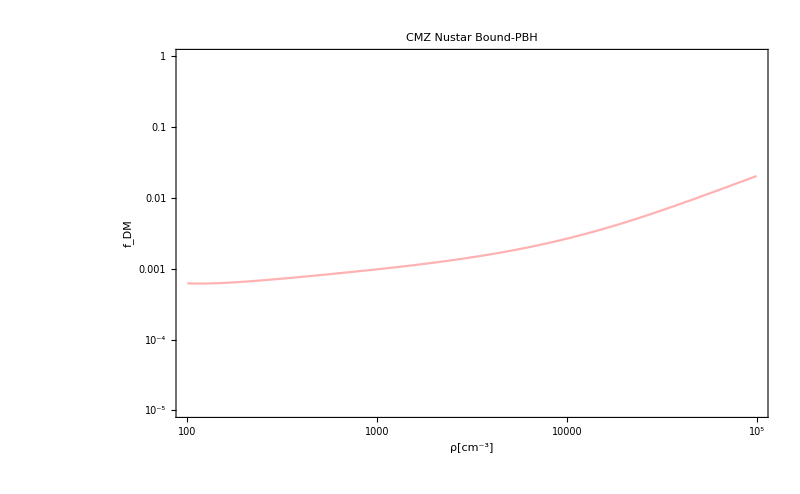

```mathematica
Legended[
LogLogPlot[
{NCloudsBoundNustarRicotti1[muvelPBH, 10, n, 0.3, 30]/NPBHCMZ
},
{n, 10^2, 10^5},
Frame->True,
PlotLabel->CMZtitlePBH, 
FrameLabel->{labelrho,labelfDM}, 
FrameTicks->{{fticksfDM, None},{fticksrho, None}},
ImageSize->800 ,
PlotStyle->{Red, Opacity[.3]},

Filling->{2-> {Top,Directive[Red, Opacity[.2]]}},


PlotRange->{{10^2,10^5}, {10^-5, 1}}
], 

 {Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 10  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 55  km/s"}],FontSize->15]],  {.85,.09}]}
]
```

```mathematica
labelPBHM=DisplayForm[StyleBox[SubscriptBox["M", "PBH"],FontSize->30]];
```

```mathematica
fticksM= Table[If[IntegerQ[i/20],{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,0,100,10}];
```

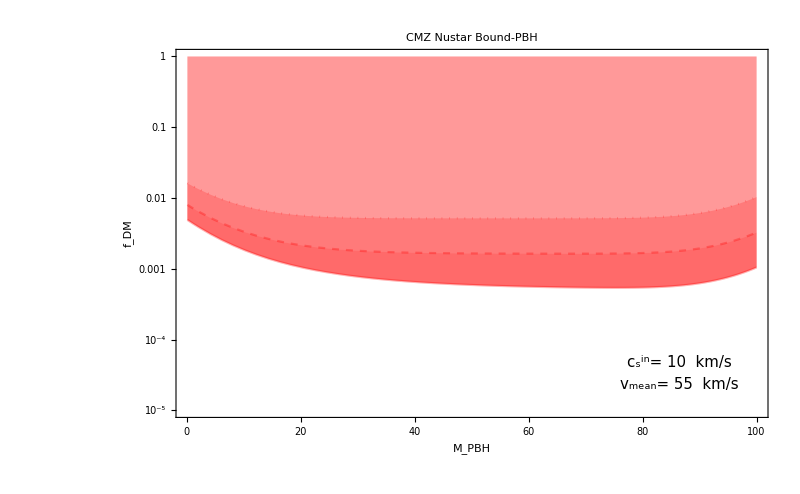

```mathematica
Legended[
LogPlot[
{NBoundNustarRicotti1PBH[muvelPBH, 10, 10^4, 0.3, m]/NPBHCMZ,
NBoundNustarRicotti1PBH[muvelPBH, 10, 10^3.5, 0.3, m]/NPBHCMZ,
NBoundNustarRicotti1PBH[muvelPBH, 10, 10^3, 0.3, m]/NPBHCMZ
},
{m, 0.1, 100},
Frame->True,
PlotLabel->CMZtitlePBH, 
FrameLabel->{labelPBHM,labelfDM}, 
FrameTicks->{{fticksfDM, None},{fticksM, None}},
ImageSize->800 ,
PlotStyle->{{Red, Opacity[.3], Dotted},{Red, Opacity[.3], Dashed}, {Red, Opacity[.3]}},

Filling->{{3-> {Top,Directive[Red, Opacity[.4]]}},{1->{{2},Directive[Red, Opacity[.2]]}} , {2->{{3},Directive[Red, Opacity[.3]]}}},


PlotRange->{{.1,100}, {10^-5, 1}}
], 

 {Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 10  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 55  km/s"}],FontSize->15]],  {.85,.09}],
Placed[Framed[linelegendn,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]}
]
```

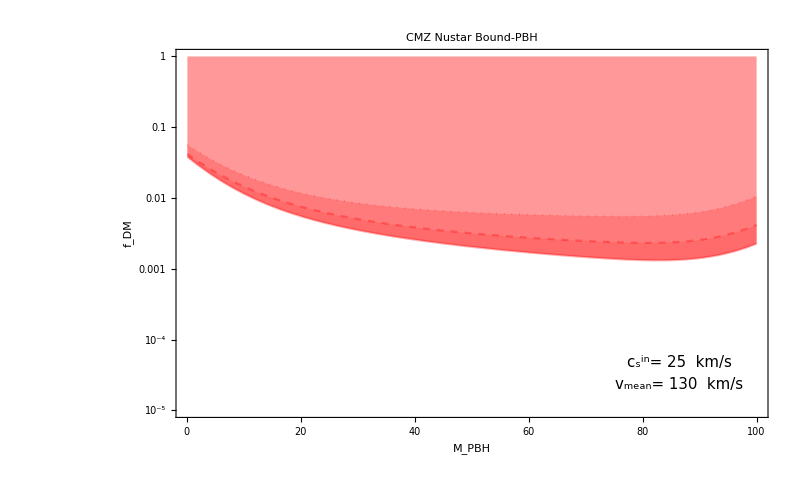

```mathematica
Legended[
LogPlot[
{NBoundNustarRicotti1PBH[130,25, 10^4, 0.3, m]/NPBHCMZ,
NBoundNustarRicotti1PBH[130,25, 10^3.5, 0.3, m]/NPBHCMZ,
NBoundNustarRicotti1PBH[130,25, 10^3, 0.3, m]/NPBHCMZ
},
{m, 0.1, 100},
Frame->True,
PlotLabel->CMZtitlePBH, 
FrameLabel->{labelPBHM,labelfDM}, 
FrameTicks->{{fticksfDM, None},{fticksM, None}},
ImageSize->800 ,
PlotStyle->{{Red, Opacity[.3], Dotted},{Red, Opacity[.3], Dashed}, {Red, Opacity[.3]}},

Filling->{{3-> {Top,Directive[Red, Opacity[.4]]}},{1->{{2},Directive[Red, Opacity[.2]]}} , {2->{{3},Directive[Red, Opacity[.3]]}}},


PlotRange->{{.1,100}, {10^-5, 1}}
], 

 {Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 25  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 130  km/s"}],FontSize->15]],  {.85,.09}],
Placed[Framed[linelegendn,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]}
]
```

```mathematica
NBoundNustarRicotti1PBH[muvelPBH, 10, 10^4, 0.3, 30]
NBoundNustarRicotti1PBH[muvelPBH, 10, 10^4, 0.3, 1]
```

{1706.55}

{4809.42}

### With monochromatic mass function